# Solar wind discontinuities and ion scattering

Abstract:

```mathematica
NotebookLocate["Anton"]
NotebookLocate["question"]
```

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
<<utilities.wl
```

```mathematica
(*(*SetOptions[$FrontEndSession,GraphicsBoxOptions->{AxesStyle->Large}]*)
(*SetOptions[ParametricPlot3D,AxesStyle->Large];*)
(*SetOptions[$FrontEndSession,GraphicsBoxOptions->{AxesStyle->{}}]*)*)
```

## Introduction

Rotational discontinuities are expected to satisfy : B_m^2+B_l^2==B_0^2==(B_(l,0))^2+(B_(m,0))^2=(κ_m^2+1)(B_(l,0))^2. 
B_l=(∇×A⃗)_m=∂A_l/∂r_n=√(-B_l^2+(B_(l,0))^2+(B_(m,0))^2)=B_0 √(1-B_l^2/B_0^2), and denote (B_(l,0):=B_(l,max)).

For B_l=B_(l,0)r_n/L, we have B_m=B_0 √(1-r_n^2/L^2(B_(l,0))^2/B_0^2)=B_0 √(1-C_1^2 r_n^2), A_l=B_0/2 (ArcSin[ C_1 r_n]/C_1+r_n √(1-C_1^2 r_n^2))

```mathematica
Integrate[√(1-Subscript[C, 1]^2 z^2),z]
```

ArcSin[z C_1]/(2 C_1)+1/2 z √(1-z^2 C_1^2)

Near neutral plane, under small B_l approximation, B_m~=B_0(1-B_l^2/B_0^2/2)

#### Magnetic field configuration

```mathematica
plotMagneticField:=Graphics3D[{
{Thick,Arrow[{{0.75,0,-0.5},{0.25,0,-0.5}}]},
Text["B_x",{0.5,0,-0.4}],
{Thick,Arrow[{{0.25,0,0.5},{0.75,0,0.5}}]},
Text["B_x",{0.5,0,0.4}],
{Thick,Arrow[{{1,0,-0.25},{1,0,0.25}}]},
Text["B_z",{0.9,0.1,0}],
{Dashed,Arrow[{{0.5,-0.25,0},{0.5,0.25,0}}]},
Text["B_y",{0.35,0.15,0}]
},
AxesLabel->{"X","Y","Z"},
Axes->True,AxesOrigin->{0,0,0},Ticks->None,
Boxed->False
]
```

## Theoretical Analysis

Notation α=ρ/L

## Deduction

Define  B_l = r_n/L B_l0; B_m=√(B_l0^2+B_m0^2)(1-B_l^2/(2(B_l0^2+B_m0^2)));B_n=B_n;
and A_l=√(B_l0^2+B_m0^2)(r_n-B_l0^2/(6 (B_l0^2+B_m0^2))r_n^3/L^2); A_m=B_n r_l-B_0 r_n^2/(2 L);A_n=0;and A⃗:= {A_l,A_m,A_n};

```mathematica
Bl =rn/L Bl0;Bm=√(Bl0^2+Bm0^2)(1-Bl^2/(2(Bl0^2+Bm0^2)));
Al=√(Bl0^2+Bm0^2)(rn-Bl0^2/(6 (Bl0^2+Bm0^2))rn^3/L^2); Am=Bn rl-Bl0 rn^2/(2 L);An=0;
vecA= {Al,Am,An};
vecB={Bl,Bm,Bn};
vecP={pl,pm,pn};
vecV=vecP-(q vecA)/c;
backgroundB={B0,0,Bn};
```

```mathematica
formRules=Join[
{rl->Subscript[r, l],rn->Subscript[r, n]},
{pl->Subscript[p, l],pm->Subscript[p, m],pn->Subscript[p, n]},
{px->Subscript[p, x],py->Subscript[p, y],pz->Subscript[p, z]},
{Bl0->Subscript[B, l,0],Bm0->Subscript[B, m,0],Bn->Subscript[B, n]},
{κm->Subscript[κ, m],κn->Subscript[κ, n]}];
```

```mathematica
Echo[vecB==vecA{rl,rm, rn}];
```

True

```mathematica
vecP={pl,pm,pn};
vecV=vecP-(q vecA)/c;
rawEq:=rawH ==1/(2m)vecV.vecV + q V/.V->0
```

#### Examine and better form

```mathematica
(*vecV/.formRules
vecB/.formRules
backgroundB/.formRules*)
```

```mathematica
(*form[x_]:=TraditionalForm@HoldForm@x
HoldForm[Subscript[B, l]=Subscript[r, n]/L Subscript[B, 0]:=Subscript[r, n]/L Subscript[B, l,max]]//form
HoldForm[Subscript[B, n]=const]//form
HoldForm[Subscript[B, m]=√(Subscript[B, l,max]^2+Subscript[B, m,0]^2-Subscript[B, l]^2)≈√(Subscript[B, 0]^2+Subscript[B, m0]^2)(1-Subscript[B, l]^2/(2(Subscript[B, 0]^2+Subscript[B, m0]^2)))]//form
HoldForm["B⃗ =∇×A⃗"]//form
HoldForm[Subscript[p, x][y]]//form
HoldForm[Subscript[v, y]]//form
HoldForm[z]//form
HoldForm[H ==1/(2m)(v⃗)^2 + q V==1/(2m)(p⃗-(q A⃗)/c)^2 + q V]//form*)
```

## Normalization

This Hamiltonian is valid for z->0.

Normalize p->p/p, r -> r/l : x=r_l/l,z=r_n/l .
We have ρ=p c/q B_(l,0). 
Shift coordinate system along x-axis to set momentum p_y=0.

We have (H m)/p^2=1/2 p_z^2+1/2(p_x-l/ρ(√((B_(l,0))^2+(B_(m,0))^2))/(B_(l,0))z +l^3/(6ρ L^2)(B_(l,0))/(√((B_(l,0))^2+(B_(m,0))^2))z^3)^2+1/2(l/ρ B_n/(B_(l,0))x -l^2/(2L ρ)z^2)^2, it is convenient to choose p= √(2H m), and

If we choose l=ρ, κ_n=B_n/(B_(l,0)), κ_m=(B_(m,0))/(B_(l,0)), and assume B_(l,0)>0
then h=1/2 p_z^2+1/2(p_x-√(κ_m^2+1)z +ρ^2/(6 L^2)1/(√(κ_m^2+1))z^3)^2+1/2(κ_n x -ρ/(2L)z^2)^2=1/2;

Denote α=ρ/L, we have

h=1/2 p_z^2+1/2(p_x-√(κ_m^2+1)z +α^2/6 1/(√(κ_m^2+1))z^3)^2+1/2(κ_n x -α/2 z^2)^2=1/2;

From observation, we have κ_m=0.5~1

{ erg, L, B_l, B_m, B_n} ➤ {h, α=ρ/L, κ_n, κ_m}

....
	If we choose l=ρ, κ_n=B_n/(B_(l,0)), κ_m=(B_(m,0))/(B_(l,0)), and assume B_(l,0)<0
	then h_–=1/2 p_z^2+1/2(p_x+√(κ_m^2+1)z -ρ^2/(6 L^2)1/(√(κ_m^2+1))z^3)^2+1/2(κ_n x -ρ/(2L)z^2)^2=1/2;
	Every solution (x, z, p_x, p_z) of h, correspond to a solution (-x, -z, -p_x, -p_z) of h,
	In other words, (x, z, p_x, p_z) satisfies h'=1/2 p_z^2+1/2(-p_x+√(κ_m^2+1)z -ρ^2/(6 L^2)1/(√(κ_m^2+1))z^3)^2+1/2(-κ_n x -ρ/(2L)z^2)^2=1/2
	it correspond to a solution (-x, z, -p_x, p_z) of h_–

```mathematica
hamiltonianEquations
```

{px'[t]==-0.01 (0.01 x[t]-z[t]^2),x'[t]==px[t]-1/2 √5 z[t]+(4 z[t]^3)/(3 √5),pz'[t]==2 z[t] (0.01 x[t]-z[t]^2)-(-(√5)/2+(4 z[t]^2)/(√5)) (px[t]-1/2 √5 z[t]+(4 z[t]^3)/(3 √5)),z'[t]==pz[t]}

```mathematica
normRules:=Join[
{rn->z l,rl->x l},
{pl->p px,pm->p py,pn->p pz},
{py->0},
{L->ρ/α,l->ρ,Bm0->κm Bl0,Bn->κn Bl0},
{ρ->(p c)/(q Bl0) }
];
case19Rules={α->1,κm->0,κn->κ};
```

```mathematica
Subscript[A, x,d]=√(Subscript[κ, m]^2+1)z -α^2/6 1/(√(Subscript[κ, m]^2+1))z^3;Subscript[A, y,d]=Subscript[κ, n] x -α/2 z^2;Subscript[A, z,d]=0;
OverVector[Subscript[A, d]] := {Subscript[A, x,d],Subscript[A, y,d],Subscript[A, z,d]};
OverVector[Subscript[A, d]]{x,y, z}
```

{z α,-(z^2 α^2)/(2 √(1+κ_m^2))+√(1+κ_m^2),κ_n}

To estimate the error for B_m far away from neutral plane B_l~=B_0

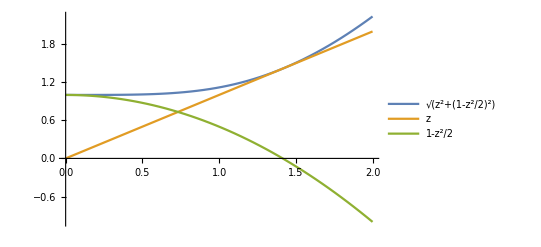

```mathematica
Plot[{√(Bl^2+Bm^2),Bl,Bm}//.normRules/.case19Rules/.{Bl0->1}//Evaluate,{z,0,2},PlotLegends->"Expressions"]
```

#### Estimation of ρ, L

As we have ρ=(p c)/(q B_0)=(√(2H m)c)/(q B_0)

```mathematica
(*ri:=QuantityMagnitude[1.02×10^2 μ^(1/2)Z^-1 T^(1/2) B^-1/.{B->(UnitConvert[B,"Gauss"]),T->(UnitConvert[T,"eV"])}]Quantity[, "Centimeters"];
thickness:=B/(Quantity[, "MagneticConstant"] jm)*)
```

```mathematica
(*(*discontinuity thickness*)
thickness/.{B->6Quantity[, "Nanoteslas"],jm->20Quantity[, "Nanoamperes"]/Quantity[, "Meters"]^2}//UnitConvert[#,"km"]&
(*proton gyro-radius*)
ri/.{B->6Quantity[, "Nanoteslas"],T->1000Quantity[, "Electronvolts"],μ->1,Z->1}//UnitConvert[#,"km"]&
(*ratio*)
√(thickness/ri)/.{B->6Quantity[, "Nanoteslas"],T->1000Quantity[, "Electronvolts"],μ->1,Z->1,jm->20Quantity[, "Nanoamperes"]/Quantity[, "Meters"]^2}*)
```

238.732415 km

537.587 km

0.666394

#### Case κ_m=0

For κ_m=0, dimensionless Hamiltonian can be further simplified as the following

Normalize p->p/p, r -> r/l. We have ρ=(p c)/(q B_0), κ=l/ρ B_n/B_0, α=ρ/L. Shift coordinate system along x to set momentum p_y=0.

We have (H m)/p^2=1/2 p_z^2+1/2(p_x-z l/ρ+z^3/6 l^3/(ρ L^2))^2+1/2(κ x -(z^2 l^2)/(2L ρ))^2, it is convenient to choose p= √(2H m), and

if we choose l=√(ρ L), h=1/2 p_z^2+1/2(p_x-z √(L/ρ)+z^3/6 √(ρ/L))^2+1/2(κ x -z^2/2)^2=1/2;

if we choose l=ρ , h=1/2 p_z^2+1/2(p_x-z +z^3/6 ρ^2/L^2)^2+1/2(κ x -z^2/2 ρ/L)^2=1/2.

#### Better Form

```mathematica
(*HoldForm[Subscript[B, l]=Subscript[r, n]/L Subscript[B, l,max]:=Subscript[r, n]/L Subscript[B, l,0]= (z l)/L Subscript[B, l,0]= z α Subscript[B, l,0]]//form
HoldForm[Subscript[B, m]=√(Subscript[B, l,max]^2+Subscript[B, m,0]^2-Subscript[B, l]^2)≈√(Subscript[B, 0]^2+Subscript[B, m0]^2)(1-Subscript[B, l]^2/(2(Subscript[B, 0]^2+Subscript[B, m0]^2)))=√(1+Subscript[κ, m]^2)(1-(z^2 α^2)/(2 (1+Subscript[κ, m]^2)))Subscript[B, 0]]//form
HoldForm[Subscript[v, y]==ⅆy/ⅆt==Subscript[p, y]-L/ρ Subscript[A, y]∼1/Subscript[κ, n](ⅆ Subscript[p, x])/ⅆt]//form
HoldForm[Subscript[z, boundary]=L/l=L/ρ=1/α]//form
HoldForm[Subscript[κ, n]=Subscript[B, n]/Subscript[B, l,max]<1]//form
HoldForm[Subscript[κ, m]=Subscript[B, m,0]/Subscript[B, l,max]]//form
HoldForm[α=Subscript[l,0]/L=(gyro radius)/(system length)]//form*)
```

## Equations

```mathematica
(*Equations*)
H:=1/2 pz[t]^2+1/2(px[t]-c1 z[t]+c2 α^2/6 z[t]^3)^2+1/2(k x[t]-α/2 z[t]^2)^2;
rawH:=H/.{k x[t]->kx,px[t]->px,z[t]->z,pz[t]->pz};
rawHH:=H/.{x[t]->x,px[t]->px,z[t]->z,pz[t]->pz}
hamiltonianEquations:={
px'[t]==-D[H, x[t]],
x'[t]==D[H, px[t]],
pz'[t]==-D[H, z[t]],
z'[t]==D[H, pz[t]]
};
initCondition:={x[0]==x0,z[0]==z0,px[0]==px0,pz[0]==pz0};
```

```mathematica
U:=rawH-1/2 pz^2;
```

### Better form

```mathematica
HoldForm[Subscript[B,m]^2=0]//form
HoldForm[Subscript[B,m]^2=const]//form
HoldForm[Subscript[B,l]^2+Subscript[B,m]^2=Subscript[B,l,max]^2]//form
HoldForm[Subscript[B,l]^2+Subscript[B,m]^2==const]//form

(*Block[{
α=α,
c1=0,c2=0,
px=Subscript[p,x],
pz=Subscript[p,z],
kx="κ_n"x,z=z},
(HoldForm[H]==rawH)//form]*)

Block[{α="α",c1=1,c2=0,px=Subscript[p,x],pz=Subscript[p,z],kx="κ_n"x,z=z},(HoldForm[H]==rawH)//form]

Block[{α="α",c1=1,c2=1,px=Subscript[p,x],pz=Subscript[p,z],kx="κ_n"x,z=z},(HoldForm[H]==rawH)//form]

Block[{α="α",c1=√(Subscript[κ, m]^2+1),c2=1/(√(Subscript[κ, m]^2+1)),px=Subscript[p,x],pz=Subscript[p,z],kx="κ_n"x,z=z},(HoldForm[H]==rawH)//form]
Block[{α="α",c1=Subscript[c,1],c2=Subscript[c,2],px=Subscript[p,x],pz=Subscript[p,z],kx="κ_n"x,z=z},(HoldForm[H]==rawH)//form]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

### Numerical Params

```mathematica
tmin=0;
tmax=2^14;
erg=1/2;
κn=k=0.01;
```

## Fast and slow variables

Because κ_n<<1, in the system, the variables κ x, p_x can be considered slow, and the variables z, p_z fast .

## Separatrix and uncertainty curve

The uncertainty curve on the phase plane (κ x, p_x) and term the separatrix on the phase plane (z, p_z)

We introduce the potential energy U(κ x,p_x,z) = H − 1/2 p_z^2 of particle motion in the phase plane (z, p_z) of fast variables

At the saddle point (z=z_c, p_z=0) of the separatrix, the potential energy U has a local maximum value; thus, ∂U/∂z = 0. We use this condition to express slow coordinates along the uncertainty curve in the plane (κ x, p_x) as functions of z_c .

```mathematica
U:=rawH-1/2 pz^2;
```

* Future work: the two solution of separatrix : Why two asymmetrical solutions?

#### Scan c1

```mathematica
tempPlot:=Block[{c1=c1temp,c2=1/c1temp,α=1},
sol=SolveValues[
(D[U, z]==0)&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
ParametricPlot[sol,{zc,-3,3},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1,N@c2]]
]

tempZoomPlot:=Block[{c1=c1temp,c2=1/c1temp,α=1},
sol=SolveValues[
(D[U, z]==0)&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
ParametricPlot[sol,{zc,-3,3},
PlotRange->{{0.9,1.05},{-0.1,0.1}},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1,N@c2]]
]

uncertaintyCurvePlot:=Block[{c1=c1temp,c2=1/c1temp,α=1},
sol=SolveValues[
(D[U, z]==0)&&D[U,{z,2}]<0&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
ParametricPlot[sol,{zc,-3,3},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1,N@c2]]
]

c1Scan:=Table[{tempPlot,tempZoomPlot,uncertaintyCurvePlot},
{c1temp,1,3/2,1/10}
]//Grid
```

#### Scan c1 and α

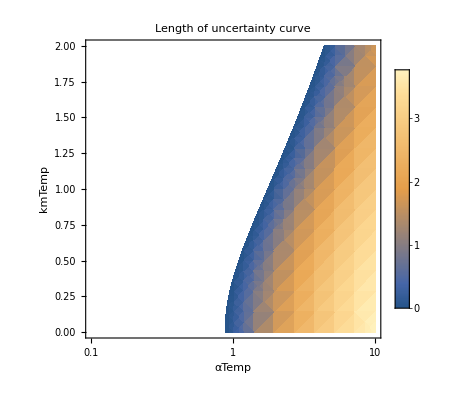

```mathematica
c1alphaScan:=DensityPlot[
arcLen[αTemp,kmTemp],{αTemp,0.1,10},{kmTemp,0,2},
ScalingFunctions->{"Log",None},
PlotLegends->Automatic,
AxesLabel->Automatic,PlotLabel->"Length of uncertainty curve"
]
(*c1alphaScan*)
```

#### Scan of both c1 and c2

```mathematica
tempPlot:=Block[{c1=c1temp,c2=c2temp,α=1},
sol=SolveValues[
(D[U, z]==0)&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
ParametricPlot[sol,{zc,-3,3},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1temp,N@c2temp]]
]

c1c2ScanU:=Table[tempPlot,
{c1temp,0,1,1/4},{c2temp,0,1,1/4}
]//GraphicsGrid//Show[#,PlotLabel->HoldForm[D[U, z] == 0]]&

uncertaintyCurvePlot:=Block[{c1=c1temp,c2=c2temp,α=1},
sol=SolveValues[
(D[U, z]==0)&&D[U,{z,2}]<0&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
ParametricPlot[sol,{zc,-3,3},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1temp,N@c2temp]]
]

c1c2ScanUC:=Table[tempPlot,
{c1temp,0,1,1/4},{c2temp,0,1,1/4}
]//GraphicsGrid//Show[#,PlotLabel->"Uncertainty Curve"]&
```

## Plane curve (κ x)^2+p_x^2==1

At neutral plane z=0

```mathematica
rawH==1/2/.{z->0}
```

kx^2/2+px^2/2+pz^2/2==1/2

we have (κ x)^2+p_x^2<=1, in other words, if (κ x)^2+p_x^2>1, the particle can not be in the neutral plane. Hence, we define the plane curve as (κ x)^2+p_x^2==1

## Plane (κ x, p_x) colored according to the type of motion in (z, p_z) plane.

Plane (κ x, p_x) colored according to the type of motion in (z, p_z) plane with frozen (κ x, p_x). Yellow denotes a single possible orbit in the  (z, p_z) plane at fixed H = 1/2, red denotes two possible orbits in the  (z, p_z) plane at fixed H = 1/2, and gray denotes the absence of solutions.

```mathematica
alphaScan:=Parallelize@Table[
Block[{α=αTemp},
ContourPlot[Length@NSolveValues[rawH==erg/. {kx->kxTemp,px->pxTemp,pz->0},z,Reals],{kxTemp,-1,7},{pxTemp,-3,3},
Contours->{0,1,2,3,4},ContourShading->{None,Gray,None,Yellow,None,Red}
]],
{αTemp,{0.1,0.3,0.5,1,10}}]
```

## Effect of v_y

da <v_y> ≃0, <v_y> !=0
∂B_x/∂z=(4π)/c j_y=(4π)/c ( j_(y,trans)+j_(y,trap)+j_(y,reg))
 j_y= ∫ f(v) v_y ⅆ v^3

## Statistically Track Particles

### TODO: Different alpha (Parameter Scanning of α)

Need to set z range to discretize the region properly

```mathematica
(*SetOptions[getPoints,InitialPoints->8*16];
SetOptions[getPoint,ReturnSolution->False];*)
```

#### α = 0.1

```mathematica
(*Block[{α=0.1},
ContourPlot[Length@NSolveValues[rawH==erg/. {kx->kxTemp,px->pxTemp,pz->0},z,Reals],{kxTemp,-2,60},{pxTemp,0,40},
Contours->{0,1,2,3,4},ContourShading->{None,Gray,None,Yellow,None,Red}
]]*)
```

```mathematica
(*alpha01=Block[{α=0.1,tmax=tmax},
x0=4./k/α;
tmax=tmax/α;
tempEqs=(rawH==erg/. {kx->k x0})&&z<-10;
regArea[]
];*)
```

```mathematica
(*alpha01
allPointsDS*)
```

```mathematica
s=allPointsDS[[8,"solution"]]//Normal//First;
tRange=Join[{t},(Values@First[s])["Domain"]//First];
Plot[Evaluate[{x[t],px[t]}/.s],tRange,PlotLegends->{"kx", "px"},AxesLabel->Automatic,PlotRange->Full]
```

Part::partd: Part specification allPointsDS⟦8,solution⟧ is longer than depth of object.

First::normal: Nonatomic expression expected at position 1 in First[allPointsDS].

Values::invrl: The argument First[allPointsDS] is not a valid Association or a list of rules.

ReplaceAll::reps: {allPointsDS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::pllim: Range specification tRange is not of the form {x, xmin, xmax}.

Plot[{x[t],px[t]}/.allPointsDS,tRange,PlotLegends→{kx,px},AxesLabel→Automatic,PlotRange→Full]

```mathematica
(*x0*)
```

#### α = 1, 10

```mathematica
(* alpha1=Block[{α=1,x0=6./k},
tempEqs=(rawH==erg/. {kx->k x0})&&z<0;
regArea[InitialRegionPlot->True]
];*)
```

```mathematica
(*alpha10=Block[{α=10,x0=6./k},
tempEqs=(rawH==erg/. {kx->k x0})&&-3<z<0;
regArea[InitialRegionPlot->True]
];*)
```

-Graphics3D-

#### Results

```mathematica
(*results=Dataset[{alpha01,alpha1,alpha10}];
results=results[All,Append[#,{
"transientRatio"->#areaOfTransientReg/#areaOfAllReg
}]&]*)
```

#### TODO : Start from positive z

```mathematica
(*alpha01P=Block[{α=0.1,x0=8./k},
tempEqs=(rawH==erg/. {kx->k x0})&&15>z>10;
regArea[]
];
 alpha1P=Block[{α=1,x0=8./k},
tempEqs=(rawH==erg/. {kx->k x0})&&z>0;
regArea[]
];
 alpha10P=Block[{α=10,x0=8./k},
tempEqs=(rawH==erg/. {kx->k x0})&&1<z<2;
regArea[]
];*)
```

```mathematica
(*results=Dataset[{alpha01P,alpha1P,alpha10P}];*)
```

### TODO?: Trapped Area (Different kappa)

TODO : Increase automatically tmax so that all particles leave the boundary

#### κ = 0.01

```mathematica
(*Block[{x0,k=0.01,tmax=2^16},
x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[InitialPoints->8*16,ReturnDataset->True];
results=nDataset[allPointsDS]
]*)
```

#### κ = 0.05

```mathematica
(*Block[{x0,k=0.05,tmax=2^16},
x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[InitialPoints->8*16,ReturnDataset->True];
results=nDataset[allPointsDS]
]*)
```

```mathematica
(*nDatasetPlot[]*)
```

```mathematica
(*results[1,"avgAreaByUTime"]
Total@results[2;;,"avgAreaByUTime"]*)
```

#### κ = 0.1

```mathematica
(*Block[{x0,k=0.1,tmax=2^16},
x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[InitialPoints->8*16,ReturnDataset->True];
results=nDataset[allPointsDS]
]*)
```

```mathematica
(*nDatasetPlot[]*)
```

```mathematica
(*results[1,"avgAreaByUTime"]
Total@results[2;;,"avgAreaByUTime"]*)
```

#### κ = 0.2

```mathematica
(*Block[{x0,k=0.2,tmax=2^16},
x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[InitialPoints->8*16,ReturnDataset->True];
results=nDataset[allPointsDS]
]*)
```

```mathematica
nDatasetPlot[]
```

nDatasetPlot[]

```mathematica
(*results[1,"avgAreaByUTime"]
Total@results[2;;,"avgAreaByUTime"]*)
```

### Trapped Area (Case Study)

#### Numerical Solving

```mathematica
(*SetOptions[getInitialPoints,InitialPoints->8*16];*)
```

```mathematica
(*Block[{x0=6/k,tmax=2^16},
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[ReturnDataset->True]
];*)
```

```mathematica
(*results=nDataset[allPointsDS]*)
```

#### Plot the Area versus numUBndPoints

```mathematica
(*plotArea[allPointsDS,Plot03->True]*)
```

```mathematica
(*nDatasetPlot[results]*)
```

```mathematica
(**)
```

### Transient Area (Parameter Scanning of κ and x_0)

```mathematica
(*SetOptions[getInitialPoints,InitialPoints->8*16];*)
```

```mathematica
(*results=Table[
Block[{k=kTemp,x0=x0temp,tmax=2^14},
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
regArea[]
],
{kTemp,{0.01,0.05,0.1,0.2}},{x0temp,4/kTemp,8/kTemp,1/kTemp}]//Flatten//Dataset;*)
```

```mathematica
(*ListPlot[{
  results[[All, {"kx", "areaOfTransientReg"}]] // Normal // Values,
  results[[All, {"kx", "areaOfTrappedReg"}]] // Normal // Values
  },
 AxesLabel -> {"κ x", "Area"},
 PlotLegends -> {"Transient", "Trapped"}
 ]

ListPlot[
results[All,{"k"->ToString}][GroupBy["k"],All,{"kx","areaOfTransientReg"}],
AxesLabel -> {"κ x", "Area"},
Joined->True,PlotMarkers->Automatic,
PlotLegends->PointLegend[Automatic,LegendLabel->"κ"],
PlotLabel->"Transient Particles"
]*)
```

## Exp 04 Scattering of pitch angle

Particles scattered by SWD can be described as θ^(n)=θ^(n-1)+Δθ(θ^(n-1);SWD), where Δθ depends on θ^(n-1) (pitch angle entering SWD) and SWD configuration (B_l, B_m, B_n), so (B_0, κ_m, κ_n, L). Where by definition L=ρ/α=(p c)/(q B_0)1/α=(√(2H m)c)/(q B_0)1/α. 	So Δθ=Δθ(θ; B_0,κ_m, κ_n, L(B_0,α;H))=Δθ(θ;B_0,κ_m, κ_n,α;H).
	Pitch angle defined as Cos[θ]==(v .B)/(|B| |v|) is dependent on SWD configuration θ=θ(κ_m, κ_n) for fixed particle (x, z, p_x, p_z). Moreover, the coordinated is also defined by SWD. 
	So to consider the effect, we define pitch angle relative to a fixed magnetic field. We call the pitch angle relative to the background magnetic field (B_m = 0, B_l = B_0) relative pitch angle (PAR). 
	Let assume that ions move in the background magnetic field, then they meet discontinuities. At the discontinuity boundaries ion pitch-angle (PA) change adiabatically to new (B_(m,0), B_(l,0)) configuration; then ions interact with discontinuity, change their pitch - angle, and this pitch - angle again can be adiabatically recalculated to (B_m = 0, B_l = B_0)  configuration.
	By adiabatic process, the magnetic moment, energy is conserved. Moreover with the assumption that the magnetic magnitude is conserved, the pitch angle also does not change. So PAR is the same as the PA calculated at the inner boundaries of the SWD.

Moreover, let assume that all discontinuities have the same constant B_m^2+B_l^2=B_0^2, same orientation (LMN coordinate is fixed to coordinates systems like GSE), but only difference in L and κ_m.
	- Our hope that for sufficiently large set of L, km values all particles will be scattered independently on SWD orientation
	- So at boundaries B_(m,0)= κ_m B_(l,0)=κ_m/(√(κ_m^2+1))B_0 and B_(l,0)= 1/(√(κ_m^2+1))B_0.

## Pitch Angle

```mathematica
(*Assumption for simplifacation*)
assums=Bl0>0 && p>0 &&
α>0 && κm>0 &&κn>0&&
x∈Reals && z∈Reals&&
px∈Reals&&pz∈Reals;
```

```mathematica
paEqRHS=Simplify[Dot[vecB,vecV]/(Norm[vecB]Norm[vecV])//.normRules,assums]
```

(p (-z^4 α^3 √(1+κm^2)+12 px z α (1+κm^2)+12 (1+κm^2) (pz-x √(1+κm^2)) κn-6 z^2 α √(1+κm^2) (1+κm^2-x α κn)))/(6 √((1+κm^2) (p^2 pz^2+(p px+(p z (z^2 α^2-6 (1+κm^2)))/(6 √(1+κm^2)))^2+p^2 (-(z^2 α)/2+x κn)^2) (z^4 α^4+4 (1+κm^2) (1+κm^2+κn^2))))

After further simplification, we can get:

```mathematica
paSWD[x_,z_,px_,pz_]:=ArcCos[(-z^4 α^3 +12 px z α √(1+κm^2)+12 √(1+κm^2) (pz-x √(1+κm^2)) κn-6 z^2 α  (1+κm^2-x α κn))/(6 √(( pz^2+(px+(z (z^2 α^2-6 (1+κm^2)))/(6 √(1+κm^2)))^2+(-(z^2 α)/2+x κn)^2) (z^4 α^4+4 (1+κm^2) (1+κm^2+κn^2))))]/Degree
```

Compare result with Anton 2019 paper: (he made a mistake:)

```mathematica
Simplify[paEqRHS/.{z->0,px->0}/.case19Rules,assums]
```

((pz-x) κ)/(√((1+κ^2) (pz^2+x^2 κ^2)))

## Scattering Map

```mathematica
scatteringPlot:=(
Join[
pxPairsPlot[allPointsDS//Select[#["stop"]=!=False&]],
paPairsPlot[allPointsDS//Select[#["stop"]=!=False&]],
pxPairsPlot[allPointsDS//Select[#stop=!=False&&#numZPoints>=1&]],
paPairsPlot[allPointsDS//Select[#stop=!=False&&#numZPoints>=1&]]
]
)

variancesPlot[pairs_List]:=(
binEdges=HistogramList[pairs//Map[First]]//First;
(*Define a function that assigns each pair to a bin based on the x-value*)
binFunction[pair_]:=Last[Select[binEdges,#<=pair[[1]]&]];
(*Use GroupBy to bin the data*)
binnedPairs=GroupBy[pairs,binFunction];

(*Define a function that calculates the variance of the y-values in a list of pairs*)varianceFunction=If[Length[#]>1,Variance[#[[All,2]]],0]&;
(*Apply this function to each bin*)
variances=Map[varianceFunction,binnedPairs]//KeySort;
ListStepPlot[variances]
)
```

```mathematica
pa=paSWD;
```

```mathematica
SetOptions[getInitialPoints,InitialPoints->1024*4];
SetOptions[getPoint,RecordzPoints->True,RecordxTurningPoints->False,RecorduBndPoints->False];
```

```mathematica
clearParams:=Clear[κm,α,κn,k,c1,c2]
```

### κ_m = 0, α=1, z>0

```mathematica
clearParams
κm=0; α=1;κn=k=0.01; 
c1=√(κm^2+1);c2=1/c1;
```

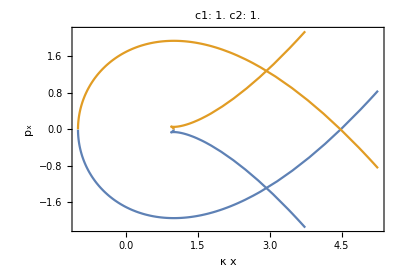

```mathematica
uCurve[3]
```

```mathematica
x0=3/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[];
```

numUBndPoints  {0}

numXTurningPoints  {0}

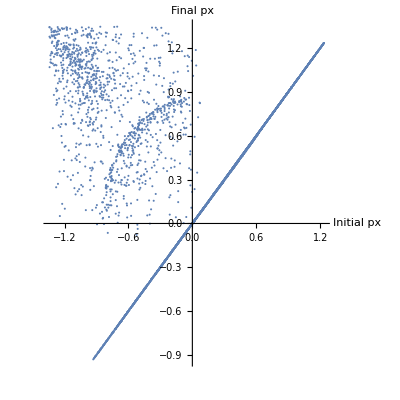
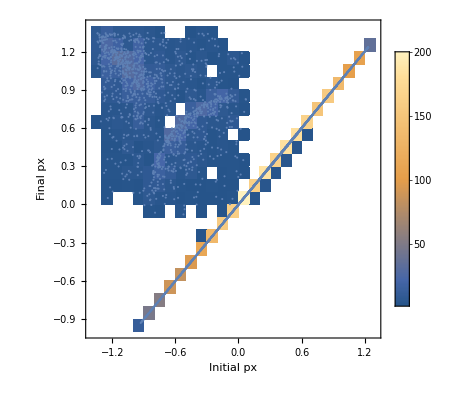
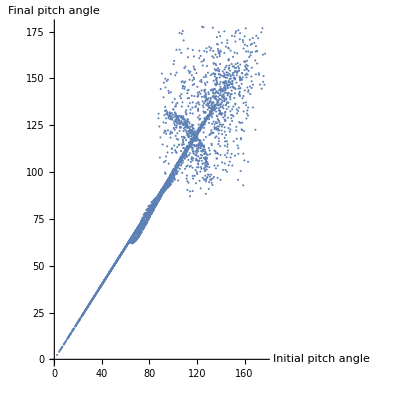
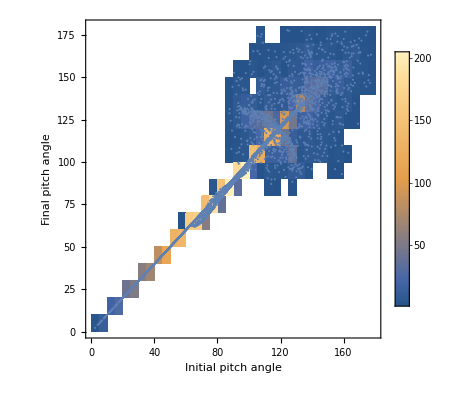
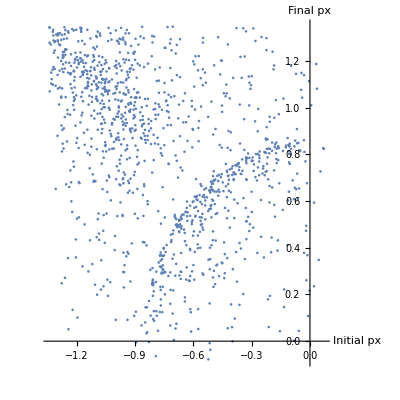
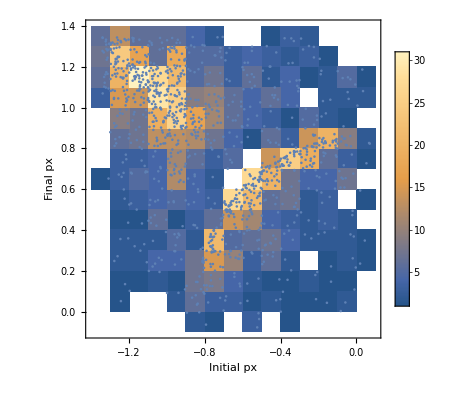
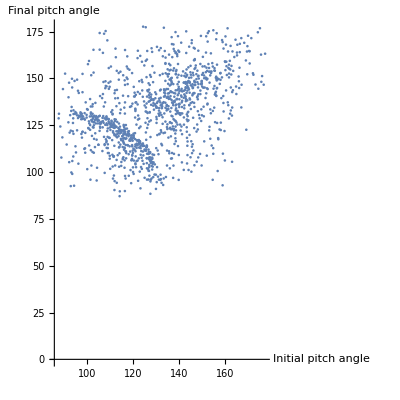
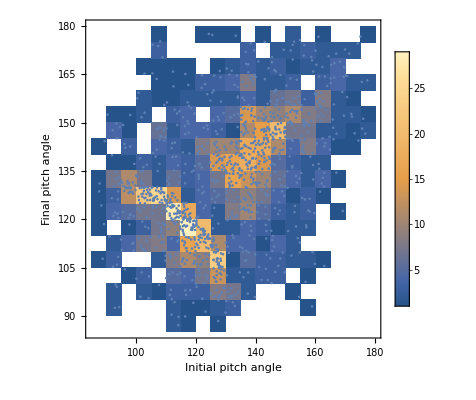

```mathematica
scatteringPlot
```

```mathematica
paTempPairs=<|"κm"->κm,"α"->α,"paPairs"->paPairs[allPointsDS//Select[#stop=!=False&&#numZPoints>=1&]]|>;
Export["paPairs00.txt",paTempPairs];
```

### κ_m = 0, α=1, z<0 (no scattering)

```mathematica
κm=0; α=1;κn=k=0.01; 
c1=√(κm^2+1);c2=1/c1;
```

```mathematica
x0=3/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[];
```

numUBndPoints  {0}

numXTurningPoints  {0}

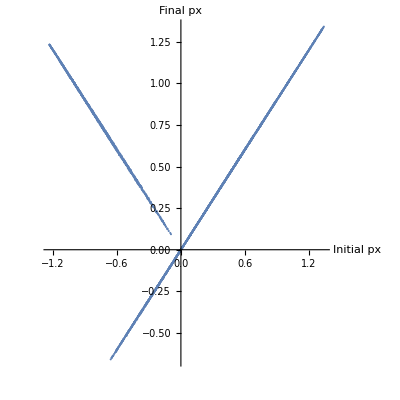
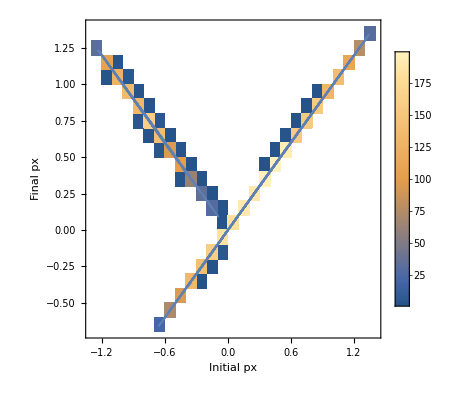
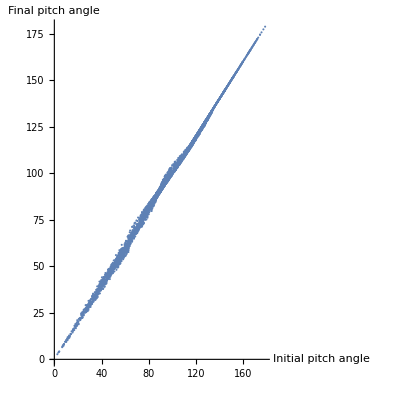
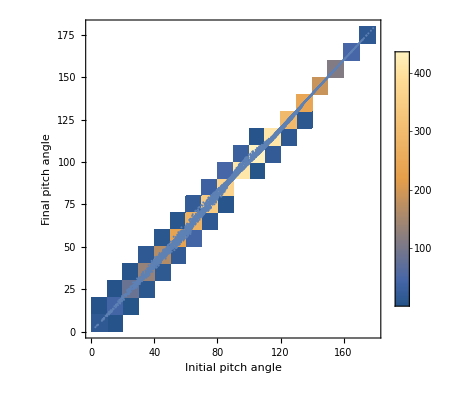
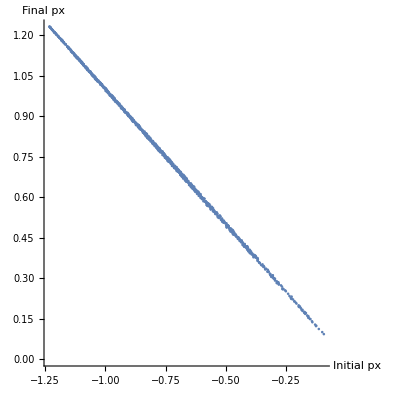
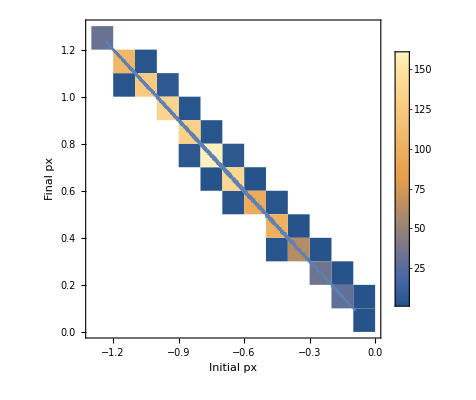
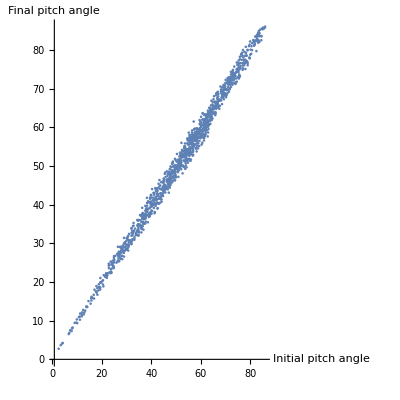
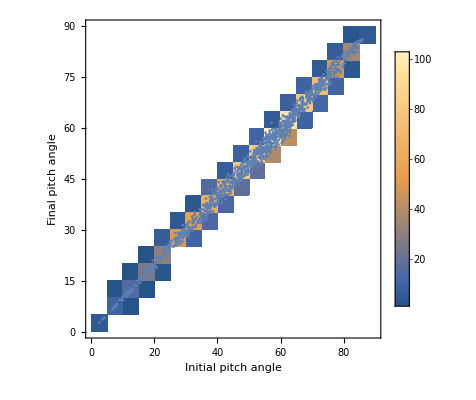

```mathematica
scatteringPlot
```

### κ_m = 1, α=1 (no scattering)

```mathematica
κm=1;
c1=√(κm^2+1);
c2=1/c1;
```

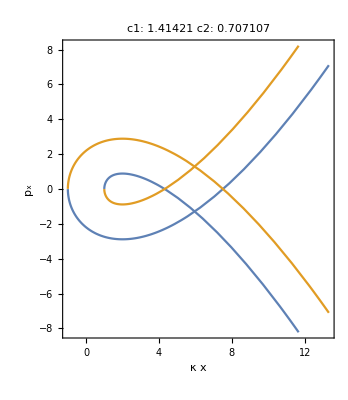

```mathematica
GraphicsRow[{uCurve[],GraphicsColumn[{uPlot[3,-2,3],uPlot[8,-2,6],uPlot[5,-1,4]}]}]
```

#### z > 0, k x0 = 8

```mathematica
(*x0=8/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[];*)
```

numUBndPoints  {0}

numXTurningPoints  {0}

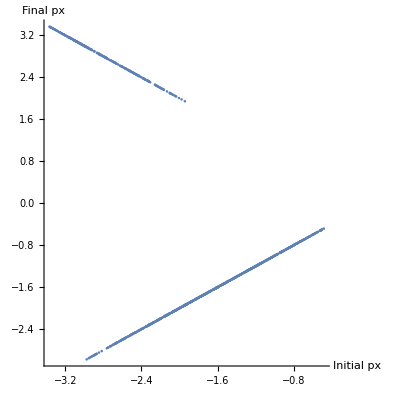
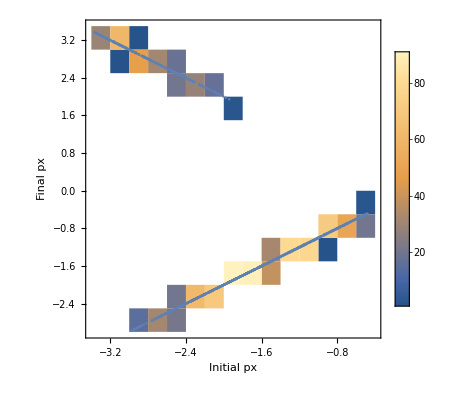
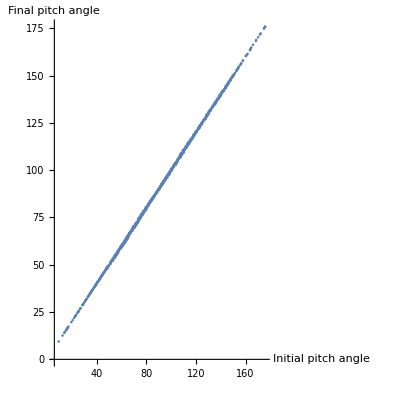
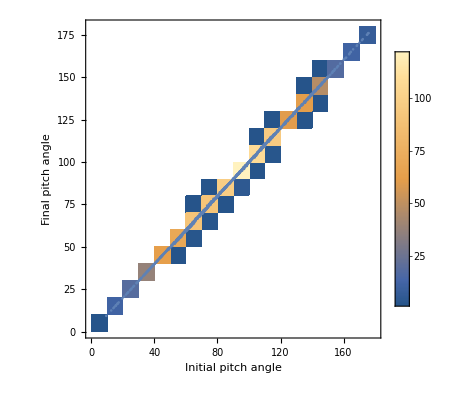
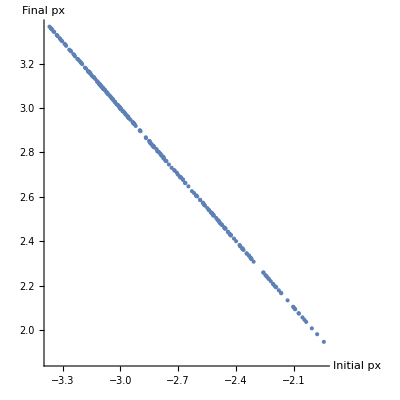
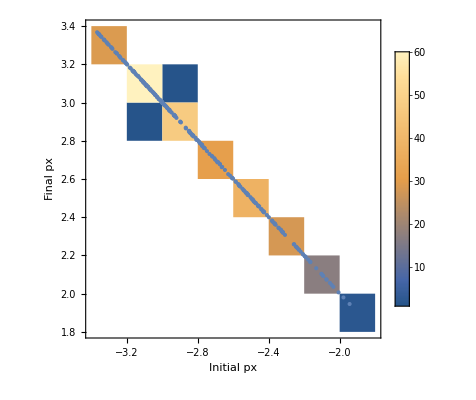
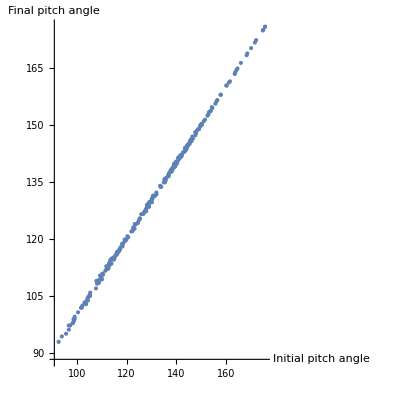
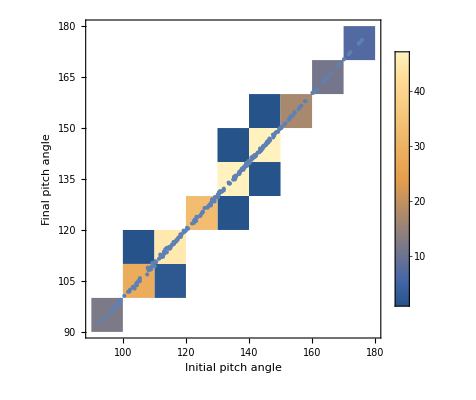

```mathematica
(*scatteringPlot*)
```

#### z < 0, k x0 = 2

```mathematica
(*x0=2/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[];*)
```

numUBndPoints  {0}

numXTurningPoints  {0}

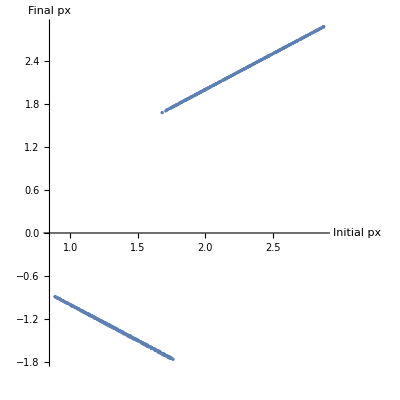
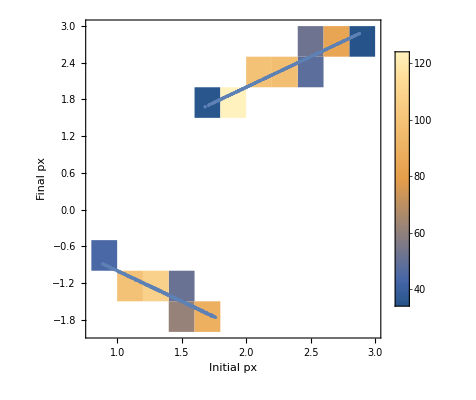
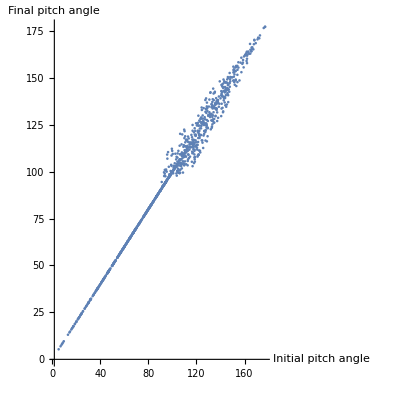
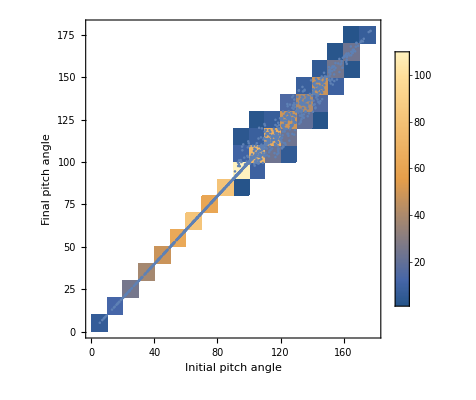
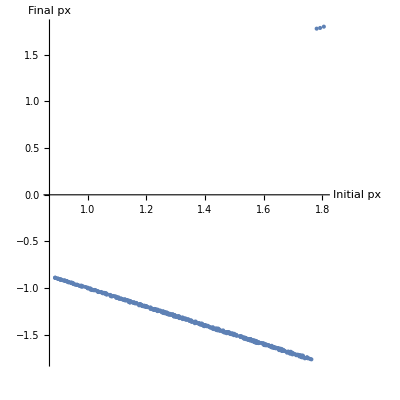
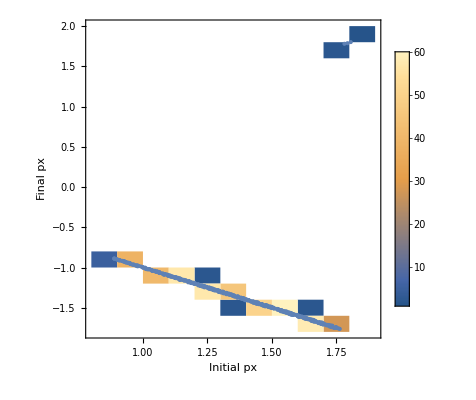
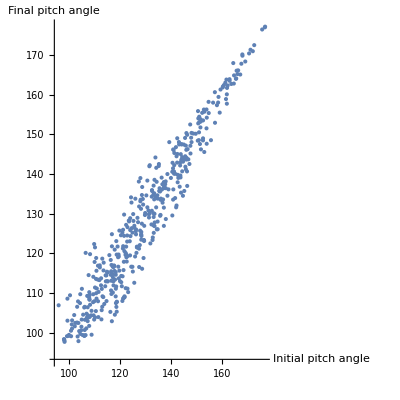
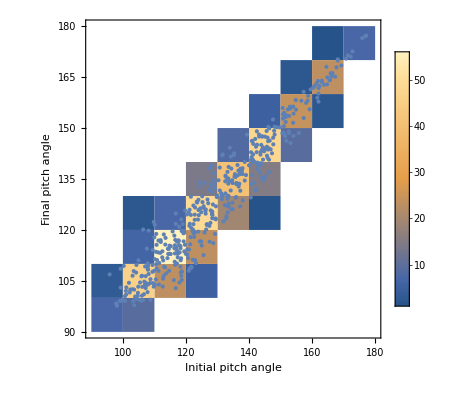

```mathematica
(*scatteringPlot*)
```

#### z < 0, k x0 = 8

```mathematica
(*x0=8/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[];*)
```

numUBndPoints  {0}

numXTurningPoints  {0}

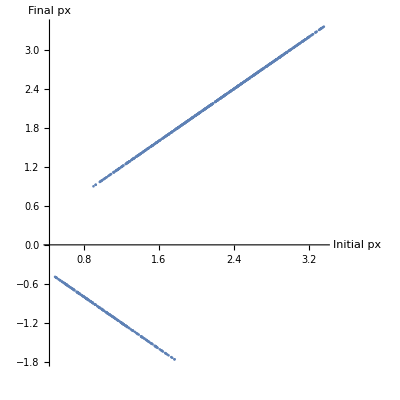
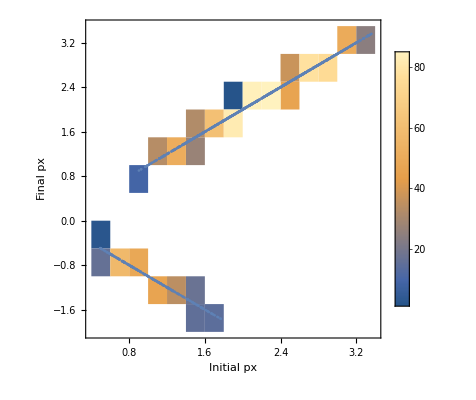
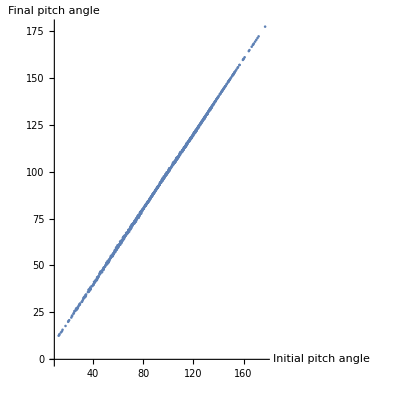
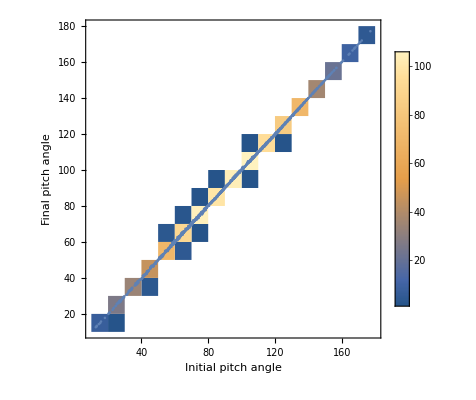
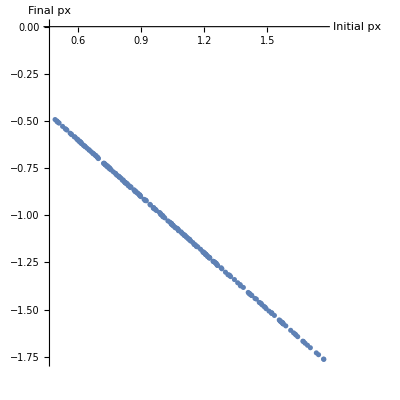
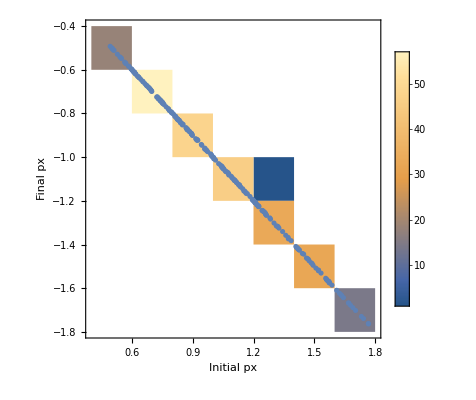
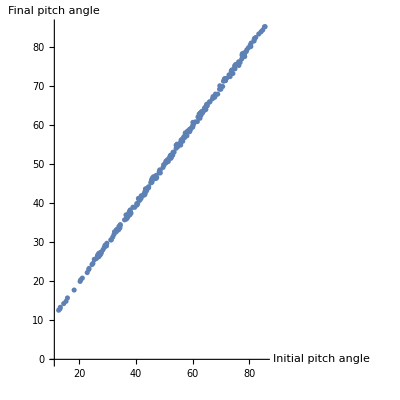
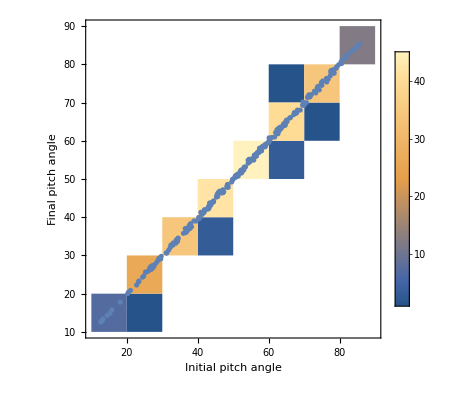

```mathematica
(*scatteringPlot*)
```

#### z < 0, k x0 = 2

```mathematica
(*x0=2/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[];*)
```

numUBndPoints  {0}

numXTurningPoints  {0}

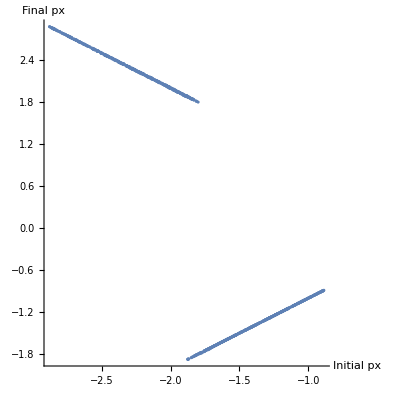
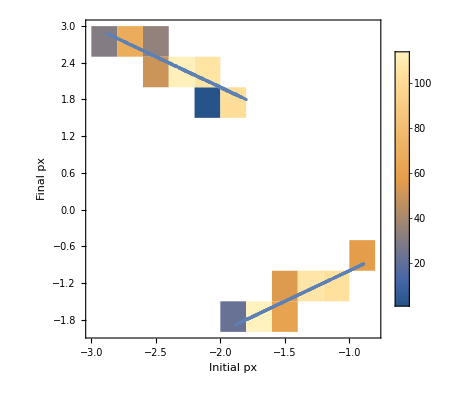
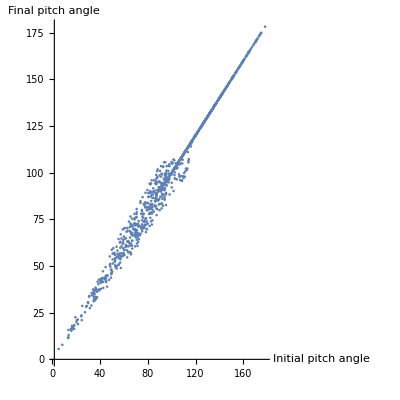
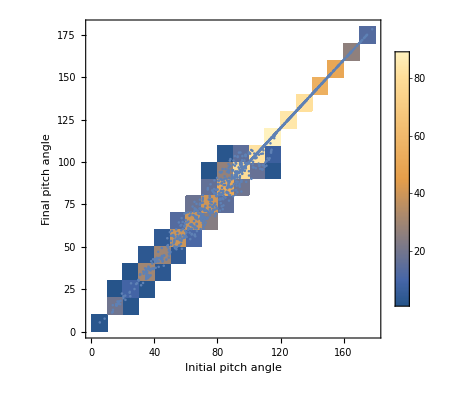
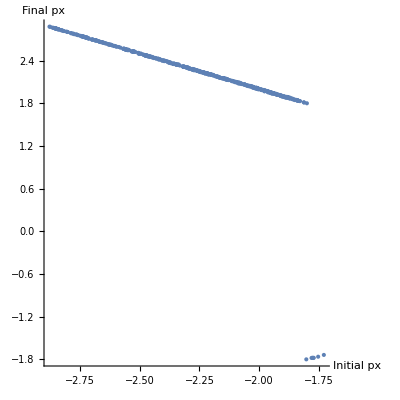
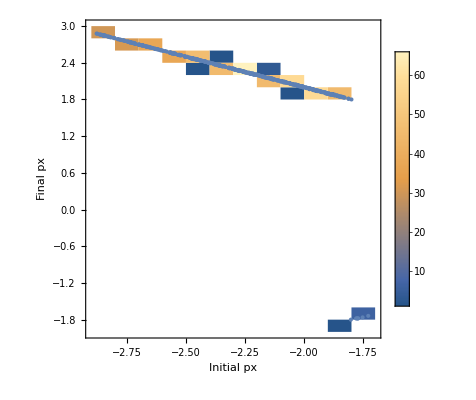
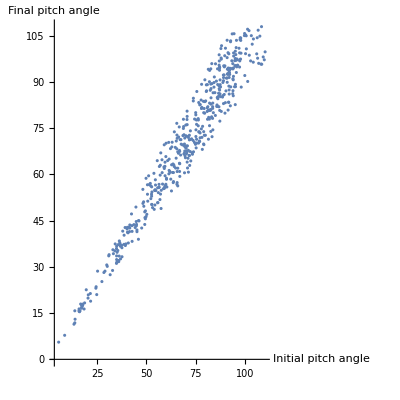
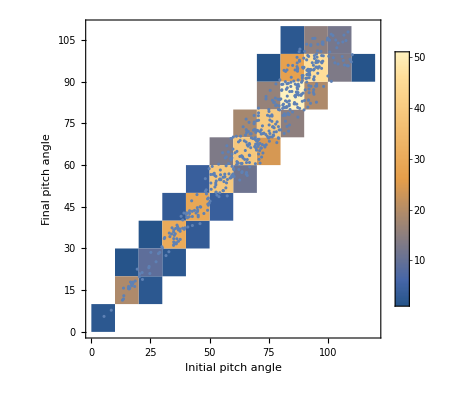

```mathematica
(*scatteringPlot*)
```

### κ_m = 1, α=2, z>0

```mathematica
clearParams
κm=1; α=2;κn=k=0.01; 
c1=√(κm^2+1);c2=1/c1;
```

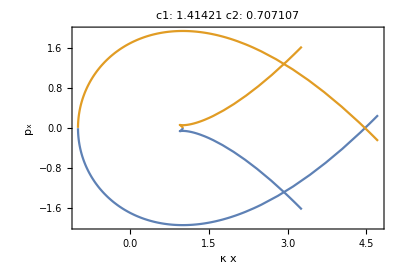

```mathematica
GraphicsRow[{uCurve[2],
GraphicsColumn[{uPlot[3,0],uPlot[3,-1],uPlot[2,-2]}]}]
```

```mathematica
x0=3/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[];
```

numUBndPoints  {0}

numXTurningPoints  {0}

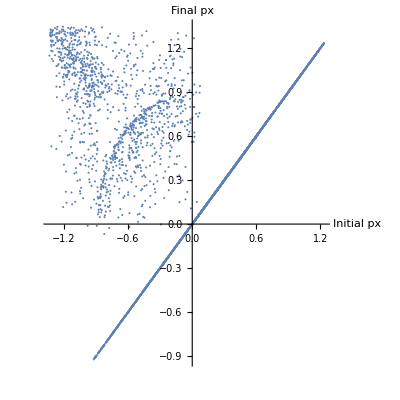
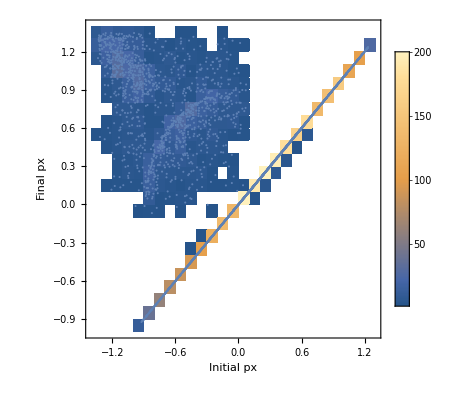
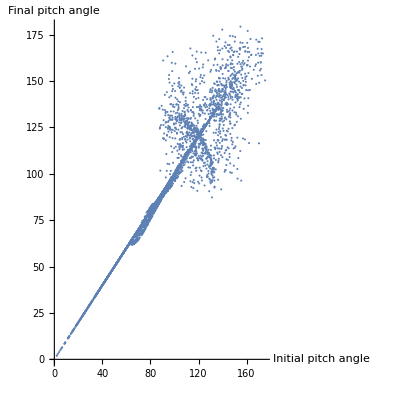
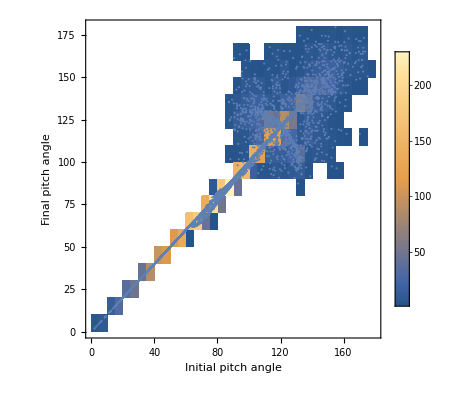
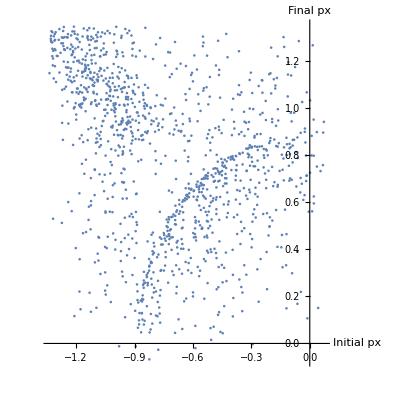
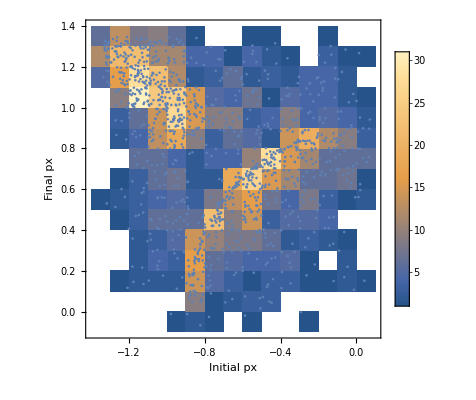
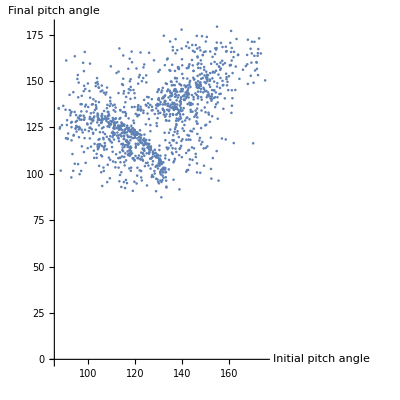
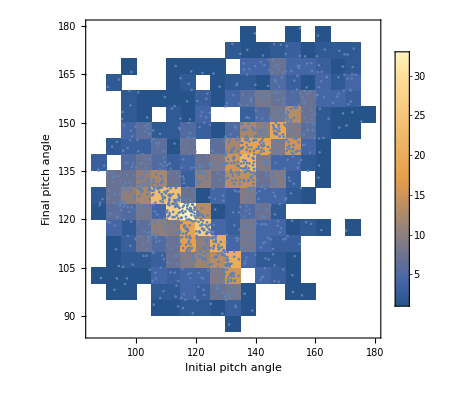

```mathematica
scatteringPlot
```

```mathematica
paTempPairs=<|"κm"->κm,"α"->α,"paPairs"->paPairs[allPointsDS//Select[#stop=!=False&&#numZPoints>=1&]]|>;
Export["paPairs01.txt",paTempPairs];
```

### κ_m = 0.5, α=2, z>0

```mathematica
clearParams
κm=1/2; α=2;κn=k=0.01; 
c1=√(κm^2+1);c2=1/c1;
```

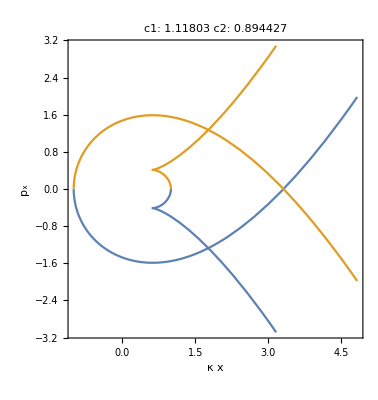

```mathematica
GraphicsRow[{uCurve[2],
GraphicsColumn[{uPlot[3,0],uPlot[3,-1],uPlot[3,-2]}]}]
```

```mathematica
x0=3/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[];
```

numUBndPoints  {0}

numXTurningPoints  {0}

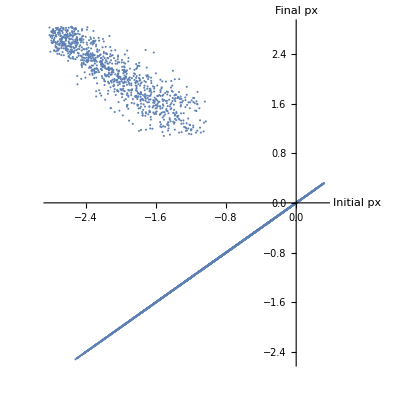
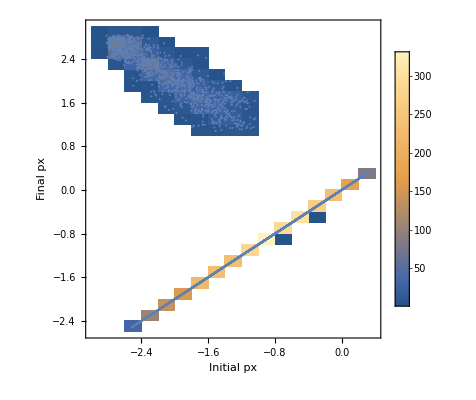
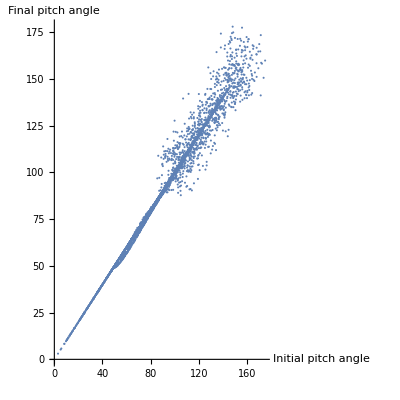
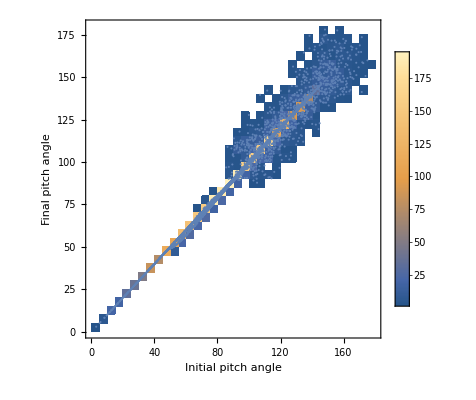
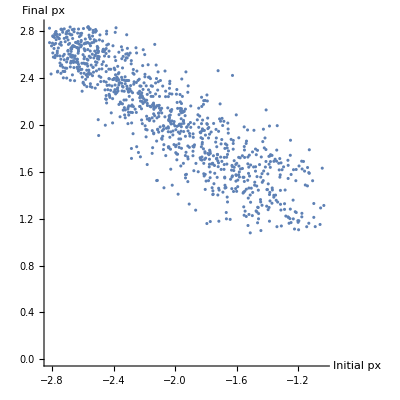
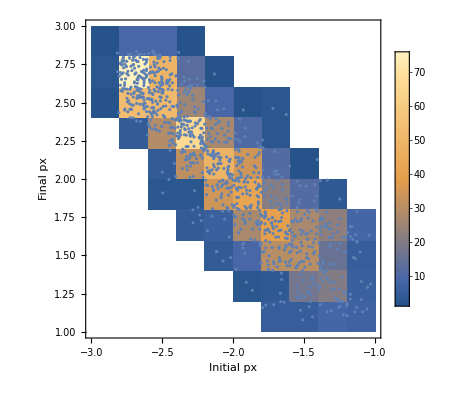
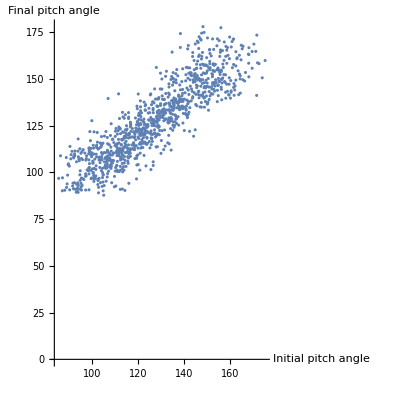
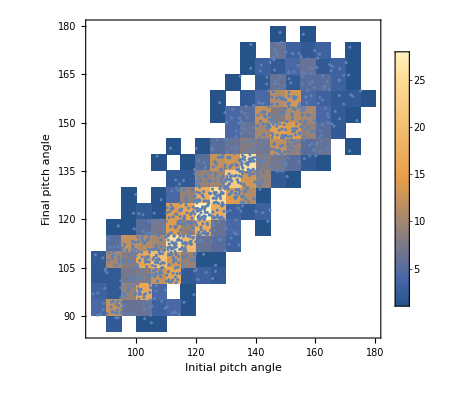

```mathematica
scatteringPlot
```

```mathematica
paTempPairs=<|"κm"->κm,"α"->α,"paPairs"->paPairs[allPointsDS//Select[#stop=!=False&&#numZPoints>=1&]]|>;
Export["paPairs02.txt",paTempPairs];
```

### κ_m = 1, α=5

Approximation reliability?
	For α=5, SWD boundaries lies at  z_b=L/l=L/ρ=1/α=0.2.

```mathematica
(*κm=1;
α=5;
c1=√(κm^2+1);
c2=1/c1;*)
```

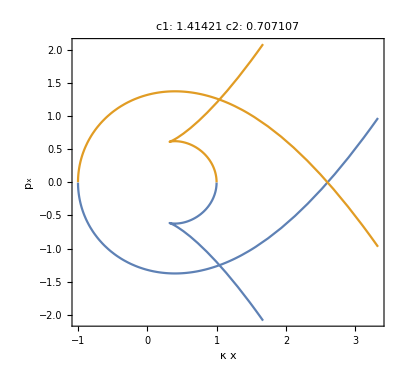

```mathematica
(*GraphicsRow[{uCurve[1],GraphicsColumn[{uPlot[2,0],uPlot[2,-1],uPlot[2,-2]}]}]*)
```

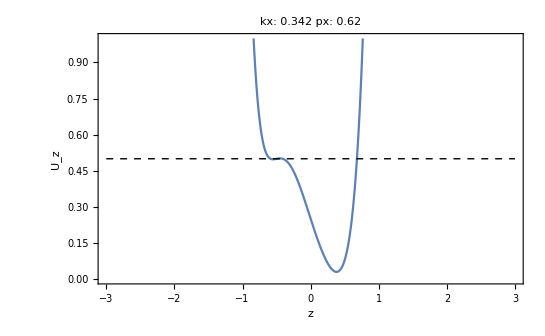

```mathematica
uPlot[0.342,0.62]
```

#### z > 0

```mathematica
x0=2/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[];
```

numUBndPoints  {0}

numXTurningPoints  {0}

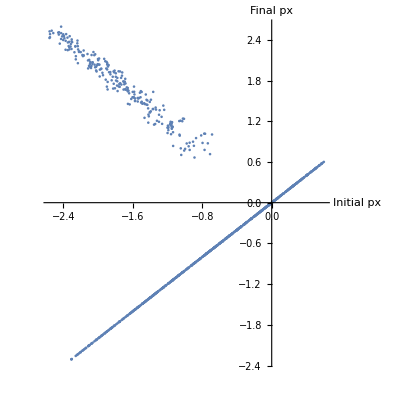
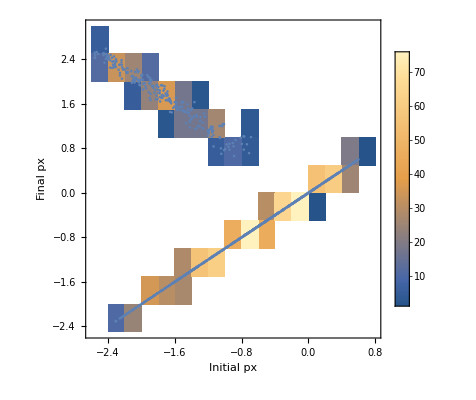
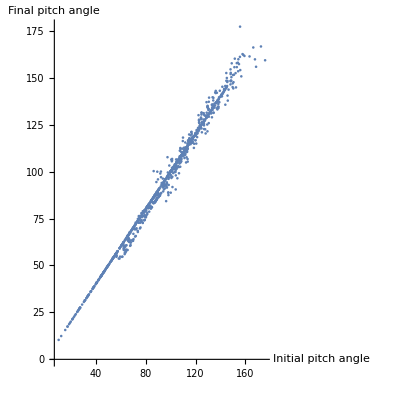
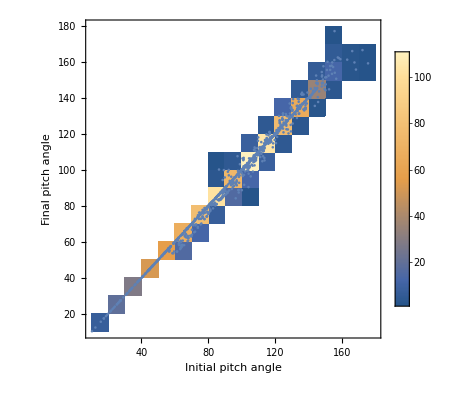
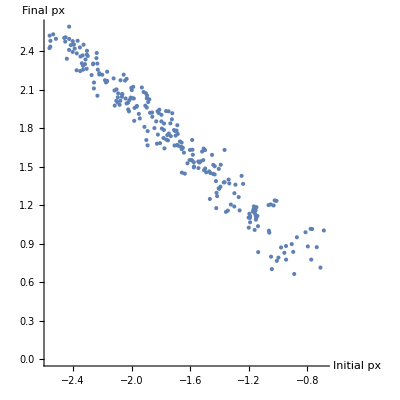
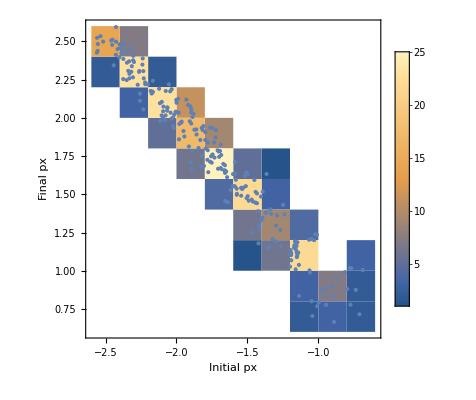
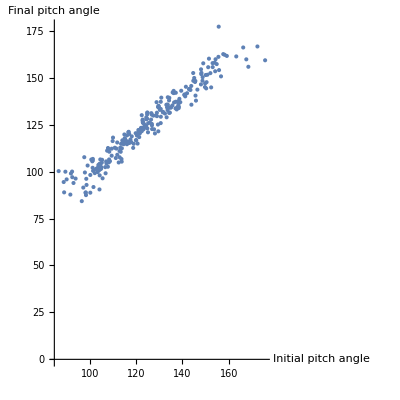
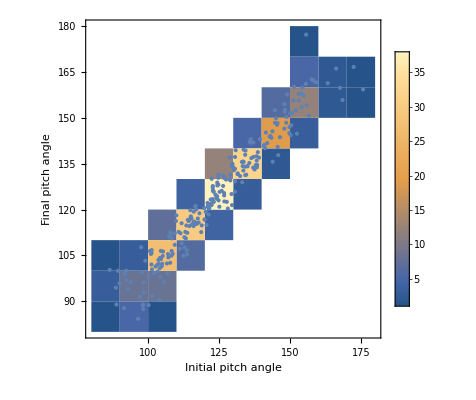

```mathematica
(*scatteringPlot*)
```

#### z < 0

```mathematica
(*x0=2/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[ReturnDataset->True];*)
```

numUBndPoints  {0}

numXTurningPoints  {0}

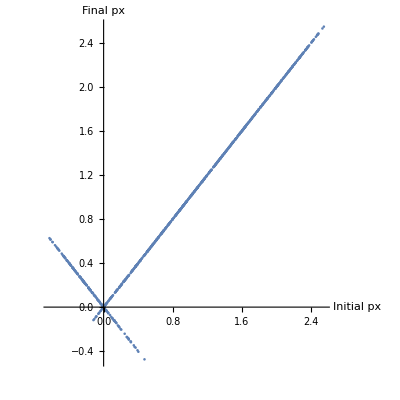
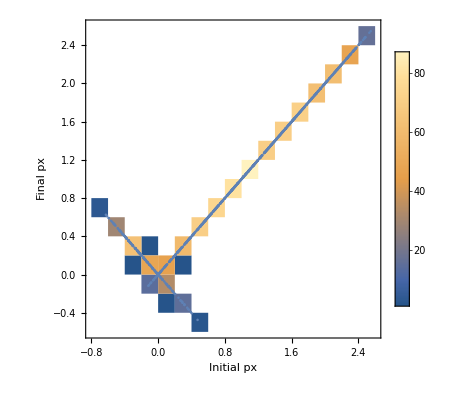
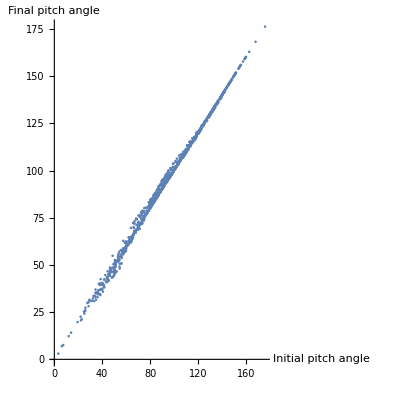
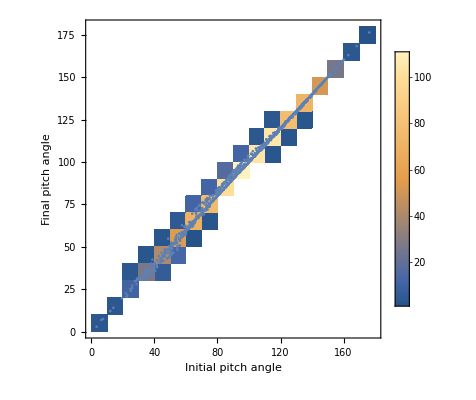
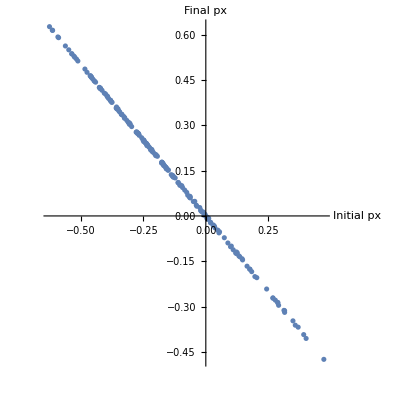
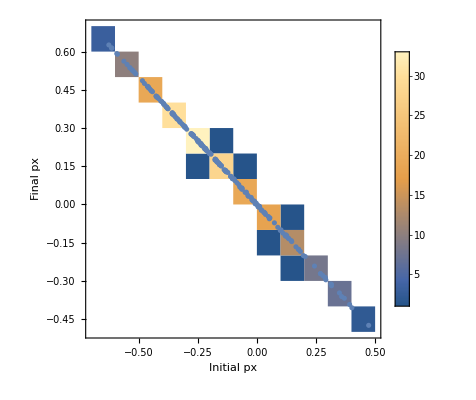
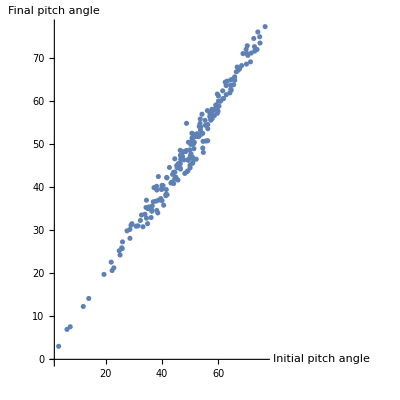
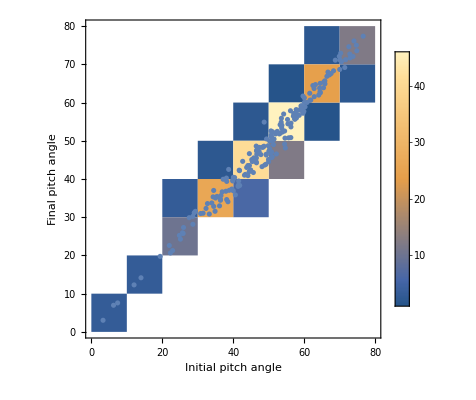

```mathematica
(*scatteringPlot*)
```

## Stochastic process

```mathematica
(*(z^3 α^2-6 z (1+κm^2)+6 (px √(1+κm^2)+pz κn))/(6 √((1+κm^2+κn^2) (pz^2+(px+(z (z^2 α^2-6 (1+κm^2)))/(6 √(1+κm^2)))^2+(-(z^2 α)/2+x κn)^2)))*)
```

Let consider one particle SWD, θ^(n)=θ^(n-1)+Δθ(θ^(n-1)).

```mathematica
(**)
```

If the last position (position means PA here) is not deterministic given the initial position, but instead has a probability distribution, you are dealing with a stochastic process . This introduces a level of complexity that cannot be handled by simple regression or interpolation methods .
A possible approach could be to model your problem as a Markov process if the state at the next step depends only on the current state and not on the sequence of events that preceded it . This is often used to model systems that change over time in a probabilistic way . Here' s an example of how you might set up a Markov process in Mathematica:

First, you need a transition matrix . This is a square matrix where each row corresponds to a starting position and each column corresponds to an ending position . Each element of the matrix is the probability of transitioning from the initial state (row) to the final state (column) .

When your initial and final conditions can be any real number from[0, 180], it means you’ re dealing with a continuous state space . This is more complex than a discrete state space, because a transition can theoretically go from any real number to any other real number, resulting in an infinite number of possibilities . One approach to handle this is to discretize your state space . This involves dividing the range[0, 180] into a certain number of discrete bins and treating any number within a certain bin as if it were the same number . The choice of how many bins to use can be a bit arbitrary and may require some trial and error .

A discrete Markov process can be seen as a random walk on a graph, where the probability of transitioning from state i to state j is specified by m⟦i,j⟧.

```mathematica
binWidth=5;
numBins=180/binWidth;
shiftedStates=Table[i-j,{i,1,numBins},{j,1,numBins}];

tmaxTemp=520;
```

```mathematica
getTransitionMatrix[file_String]:=(
paPairsTemp=Import[file]//ToExpression;

(*data=RandomReal[{0,180},{1000,2}];*)
data=paPairsTemp["paPairs"];

{bins,pdf}=HistogramList[data,{0,180,binWidth},"PDF"];

proc=DiscreteMarkovProcess[p0,pdf];

(*Get the transition matrix of the Markov process*)
transitionMatrix=N@MarkovProcessProperties[proc,"TransitionMatrix"]
)
```

```mathematica
(*Define a function to calculate the variance at time t*)
variance[t_]:=(
(*Calculate the state probabilities at time t*)
probabilities=probabilitiesTime[t];

(*Shift the states by the initial state for calculating moments*)
(*Calculate the first and second moments*)
firstMoment=p0 . Diagonal[probabilities . shiftedStates];
secondMoment=p0 . Diagonal[probabilities . (shiftedStates^2)];
(*Return the variance:second moment-(first moment)^2*)
secondMoment-firstMoment^2
)
```

#### Scattered by one SWD again, again and again. Markov process is time - homogeneous (i . e ., the transition matrix is the same at every time step)

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

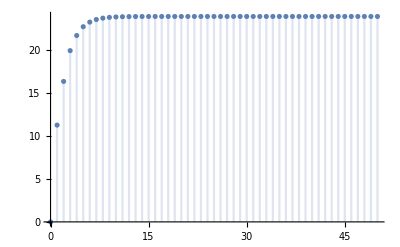

```mathematica
p0=ConstantArray[1/numBins,numBins];

(*Get the transition matrix of the Markov process*)
transitionMatrix=getTransitionMatrix["paPairs00.txt"];

ClearAll[probabilitiesTime]
probabilitiesTime[0]=IdentityMatrix[numBins];
probabilitiesTime[t_Integer?Positive]:=probabilitiesTime[t]=probabilitiesTime[t-1].transitionMatrix;

DiscretePlot[variance[t],{t,0,tmaxTemp}]
```

#### Scattered by multiple SWDs

```mathematica
FlipMatrix[matrix_]:=Module[{dim=Dimensions[matrix][[1]]},Table[matrix[[dim+1-i,dim+1-j]],{i,1,dim},{j,1,dim}]]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

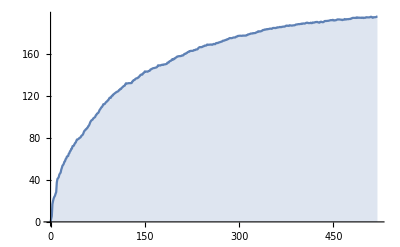

```mathematica
p0=ConstantArray[1/numBins,numBins];

(*Define the transition matrix function to change with time*)
transitionMatrixs=getTransitionMatrix/@FileNames["paPairs*"];
flippedMatrixs=Map[FlipMatrix,transitionMatrixs]; (*Flip each matrix in the list*)
transitionMatrixsAll=Join[transitionMatrixs,flippedMatrixs];(*Join original and flipped matrices*)
transitionMatrixsRandom=RandomChoice[transitionMatrixsAll,tmaxTemp];

(*Create a function that memoizes matrix powers*)
ClearAll[probabilitiesTime]
probabilitiesTime[0]=IdentityMatrix[numBins];
probabilitiesTime[t_Integer?Positive]:=probabilitiesTime[t]=probabilitiesTime[t-1].transitionMatrixsRandom[[t]];

DiscretePlot[variance[t],{t,0,tmaxTemp}]
```

Looked at into one specific pitch angle

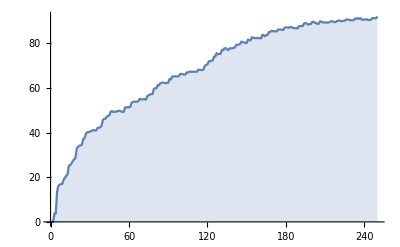

```mathematica
i0=17;
p0=UnitVector[numBins,i0];
DiscretePlot[variance[t],{t,0,tmaxTemp}]
```

## Exp 03 c_2=1/c_1

```mathematica
(*c1=5/4;
c2=1/c1;*)
```

### Pre Analysis

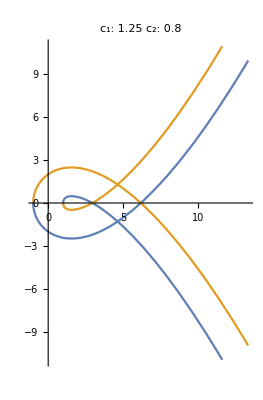

```mathematica
(*sol=SolveValues[
(∂_z U==0)&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
ParametricPlot[sol,{zc,-5,5},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1,N@c2]]//Print;*)
```

1/2 (0.5-z^2/2)^2+1/2 (-(5 z)/4+(2 z^3)/15)^2

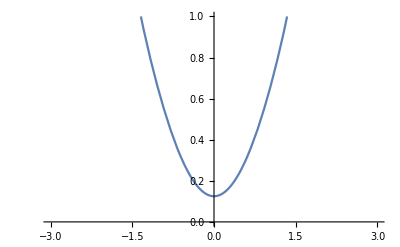

```mathematica
(*tempU=U/.{kx->0.5,px->0}
Plot[tempU,{z,-3,3},PlotRange->{0,1}]*)
```

1/2 (2-z^2/2)^2+1/2 (1-(5 z)/4+(2 z^3)/15)^2

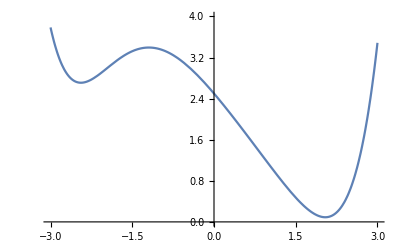

```mathematica
(*tempU=U/.{kx->2,px->1}
Plot[tempU,{z,-3,3},PlotRange->{0,4}]*)
```

1/2 (4-z^2/2)^2+1/2 (1-(5 z)/4+(2 z^3)/15)^2

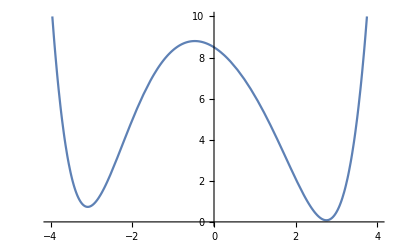

```mathematica
(*tempU=U/.{kx->4,px->1}
Plot[tempU,{z,-4,4},PlotRange->{0,10}]*)
```

1/2 (4-z^2/2)^2+1/2 (-(5 z)/4+(2 z^3)/15)^2

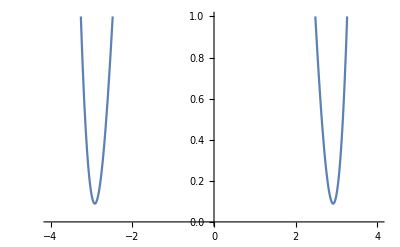

```mathematica
(*tempU=U/.{kx->4,px->0}
Plot[tempU,{z,-4,4},PlotRange->{0,1}]*)
```

1/2 (8-z^2/2)^2+1/2 (-3-(5 z)/4+(2 z^3)/15)^2

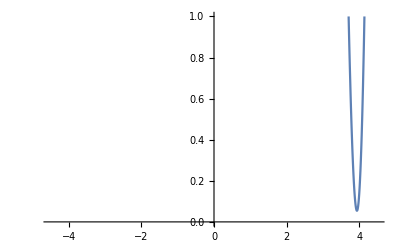

```mathematica
(*tempU=U/.{kx->8,px->-3}
Plot[tempU,{z,-4.5,4.5},PlotRange->{0,1}]*)
```

```mathematica
(*SetOptions[getInitialPoints,InitialPoints->8*32];
SetOptions[plotArea,TrappedStandard->2];
SetOptions[ListPlot,PlotRange->All];*)
```

### Launched from neutral plane : z=0

```mathematica
(*SetOptions[getInitialPoints,InitialPoints->8*8];*)
```

```mathematica
(*rawHH*)
```

pz^2/2+1/2 (0.01 x-z^2/2)^2+1/2 (px-(5 z)/4+(2 z^3)/15)^2

```mathematica
(*c1=5/4;
c2=1/c1;
tempEqs=(rawHH/. {z->0})==erg*)
```

px^2/2+pz^2/2+0.00005 x^2==1/2

```mathematica
(*Block[{c1,c2,x0,farBoundary=10},
c1=5/4;
c2=1/c1;
tempEqs=(rawHH/. {z->0})==erg;
allPointsDS=getPoints[StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnDataset->True];
]*)
```

```mathematica
(*plotArea[allPointsDS]*)
```

-Graphics-

#### Inspect some trajectories

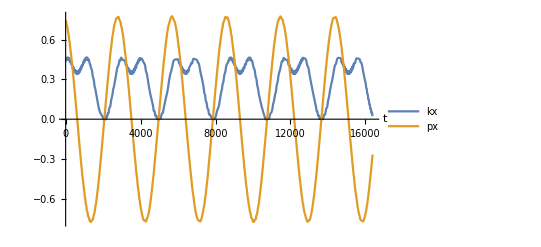
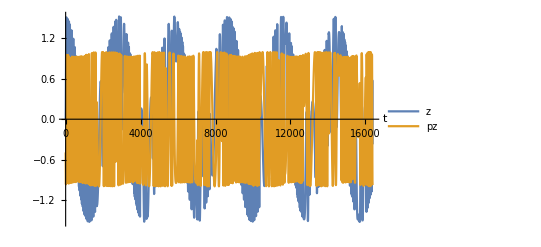
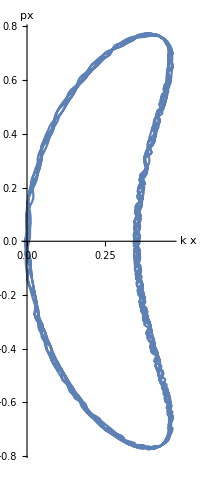

```mathematica
(*Block[{c1,c2,x0,farBoundary=10},
c1=5/4;
c2=1/c1;
x0=8/k;
initialPoint=allPointsDS//Select[#numUBndPoints==0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

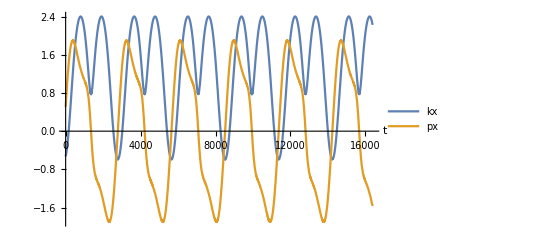
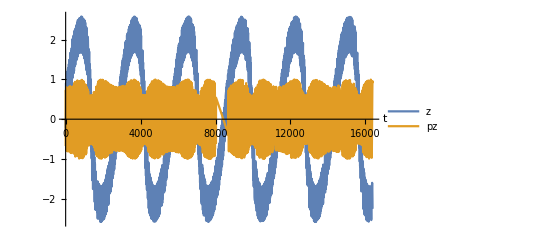
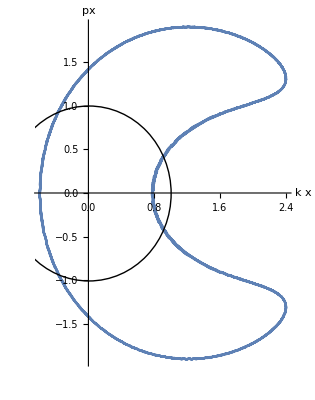

```mathematica
(*Block[{c1,c2,x0,farBoundary=10},
c1=5/4;
c2=1/c1;
x0=8/k;
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop==False&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

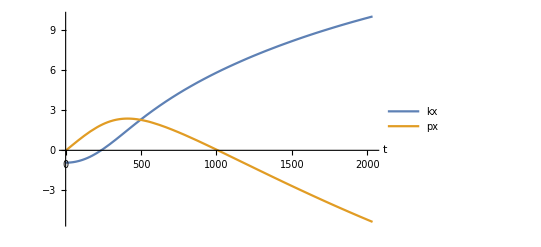
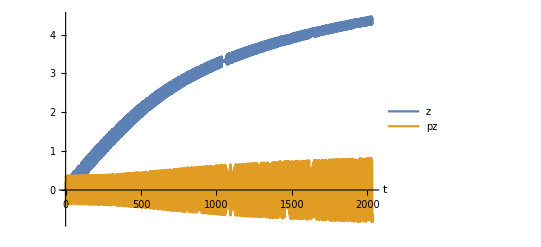
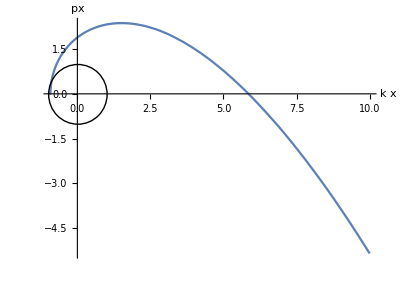

```mathematica
(*Block[{c1,c2,x0,farBoundary=10},
c1=5/4;
c2=1/c1;
x0=8/k;
initialPoint=allPointsDS//Select[#numUBndPoints==1&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

### Launched above neutral plane : z < 0

```mathematica
(*Block[{c1,c2,x0},
c1=5/4;
c2=1/c1;
x0=8/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[ReturnDataset->True];
]*)
```

```mathematica
(*plotArea[allPointsDS]*)
```

No non-stop particles

No trapped particles

-Graphics-

#### Inspect some trajectories

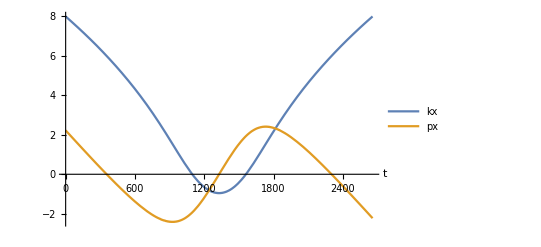
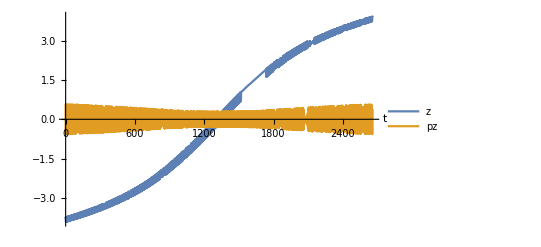
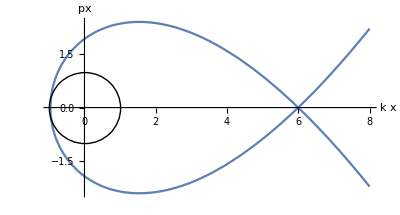
{-Graphics-,-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
(*Block[{c1,c2},
c1=5/4;
c2=1/c1;
initialPoint=allPointsDS//Select[#numUBndPoints==2&]//First//Part[#,"initialPoint"]&//Normal;
sol=getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True];
]*)
```

### Launched above neutral plane : z > 0

```mathematica
(*Block[{c1,c2,x0},
c1=5/4;
c2=1/c1;
x0=8/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[ReturnDataset->True];
]*)
```

```mathematica
(*plotArea[allPointsDS]*)
```

No non-stop particles

No trapped particles

-Graphics-

#### Inspect some trajectories

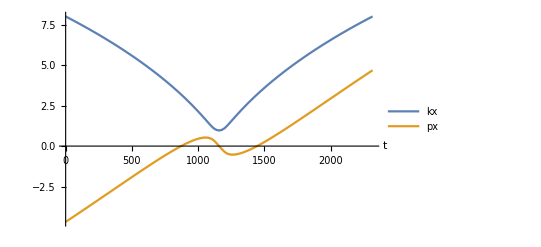
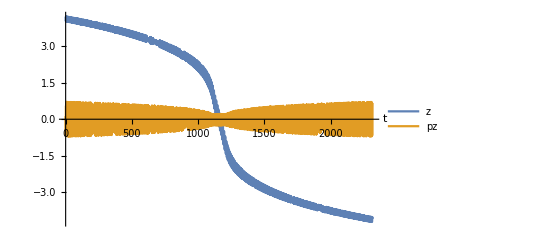
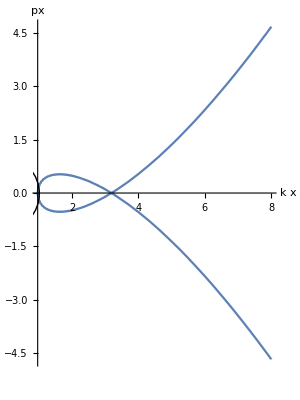
{-Graphics-,-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
(*Block[{c1,c2},
c1=5/4;
c2=1/c1;
initialPoint=allPointsDS//Select[#numUBndPoints==2&]//First//Part[#,"initialPoint"]&//Normal;
sol=getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True];
]*)
```

### Results

No trapped particles when launched from above and below

## Exp 02 (Standard Case, Anton 2020)

```mathematica
(*c1=1;
c2=1;*)
```

Anton 2020 paper consider three populations of trajectories in the (κ x, p_x) plane. 
	(i) regular trajectories never approaching uncertainty curve with I_z ≈ const [in the (κ x, p_x)  plane these trajectories occupy region located to the left from uncertainty curve] and
	(ii) transient trajectories reflecting from uncertainty curve. Due to geometrical I_z jumps trajectories of this latter population are characterized by rapid destruction of I_z invariant
	(iii) quasiregular trajectories: consists of ion trajectories that cross uncertainty curve.

Anton 2013 paper describe two populations
	(1) trapped: motion is bounded.
	(2) transient: motion becomes unbounded.

The caveat here is to choose the max-time to NDSolve
	larger t-max means more transient particles (some particles may go around for multiple orbits then suddenly become transient because of scattering)

### Pre Analysis

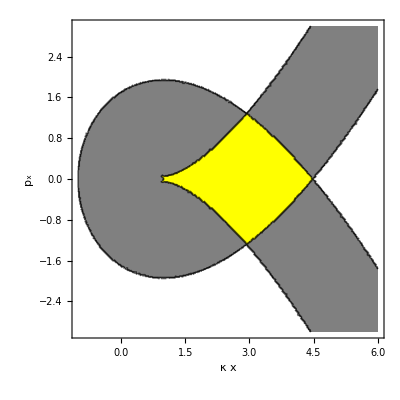

```mathematica
(*GraphicsRow[{uCurveContourPlot[],GraphicsColumn[{uPlot[0.5,0,2],uPlot[1.25,0,2.5],uPlot[5,1,4]}]}]*)
```

### Launched from neutral plane : z=0

```mathematica
(*SetOptions[getInitialPoints,InitialPoints->64];
SetOptions[getPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True];
SetOptions[NDSolve,PrecisionGoal->∞];
z0=0;farBoundary=6;
tmax=2^13;*)
```

```mathematica
(*tempEqs=(rawHH/. {z->z0})==erg;
allPointsDS=getPoints[];*)
```

numUBndPoints  {0,1,3,5,7,8,9,11,15,17,23,24,27,30,31,32,36,38,40,62,66,126}

numXTurningPoints  {0,1,2,3,4,6,7,8,9,11,12,13,14,15,16,17,18,19,21,25,26,30,34,35,37,42}

```mathematica
(*plotArea[allPointsDS,TrappedStandard->1,Graphis->True]*)
```

-Graphics-

#### Inspect some trajectories

```mathematica
(*(*Transient*) 
initialPoint={-1.5025252334999792,0.9629729196455636,0,-0.2607573242705105};
(*Trapped*)
 initialPoint={-67.31197000404433,0.6835510571236819,0,0.2805781476512689} ;
(*Regular*)
initialPoint={17.273533628917143,0.7981077113243987,0,0.5697993933102234}
sol=getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True,Graphis->False]*)
```

{17.2735,0.798108,0,0.569799}

```mathematica
(*stopPoints=allPointsDS//Select[#numZPoints>0&]//Select[#stop>0&];
initialPoint=stopPoints//RandomChoice//Part[#,"initialPoint"]&//Normal;
sol=getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True,Graphis->False]*)
```

```mathematica
(*nonStopPoints=allPointsDS//Select[#numZPoints>0&]//Select[#stop==False&];
initialPoint=nonStopPoints//RandomChoice//Part[#,"initialPoint"]&//Normal;
sol=getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True,Graphis->False]*)
```

#### Based on numUBndPoints

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints==0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol,PlotVy->True,Plot3D->True]
]*)
```

-Graphics-

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints==1&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True,PrecisionGoal->∞]["solution"];
overviewPlot[sol,PlotVy->True,Plot3D->True]
]*)
```

-Graphics-

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop==False&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol,PlotVy->True,Plot3D->True]
]*)
```

-Graphics-

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop>0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True,PrecisionGoal->∞]["solution"];
overviewPlot[sol,PlotVy->True,Plot3D->True]
]*)
```

-Graphics-

### Launched above neutral plane : z>0

```mathematica
(*x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[InitialPoints->64,ReturnDataset->True];*)
```

numUBndPoints  {0,24}

numXTurningPoints  {0,26}

No transient particles

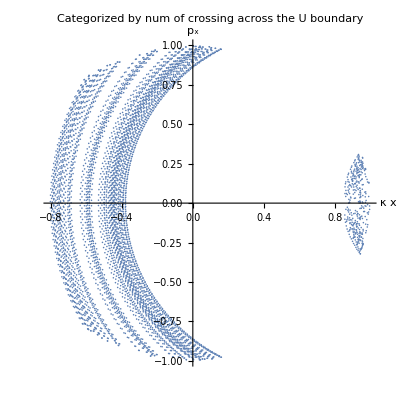
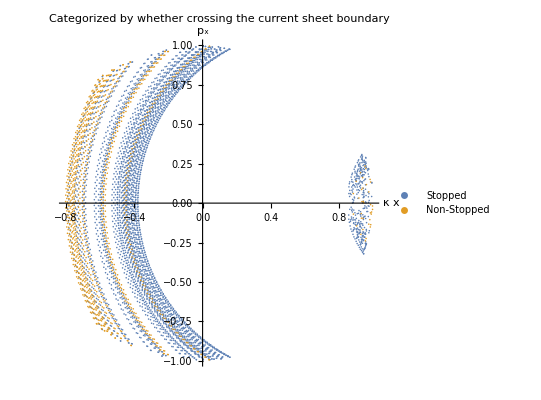

```mathematica
(*plotArea[allPointsDS]*)
```

#### Inspect some trajectories

```mathematica
(*initialPoint=allPointsDS//Select[#numZPoints>0&]//Select[#stop==False&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol]*)
```

-Graphics-

```mathematica
(*initialPoint=allPointsDS//Select[#numZPoints>0&]//Select[#stop>0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol]*)
```

-Graphics-

```mathematica
(*initialPoint=allPointsDS//Select[#numZPoints==0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol]*)
```

-Graphics-

### Launched below neutral plane: z<0

```mathematica
(*x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[ReturnDataset->True];*)
```

```mathematica
(*plotArea[allPointsDS]*)
```

#### Inspect some trajectories

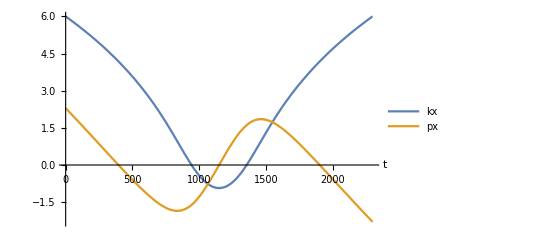
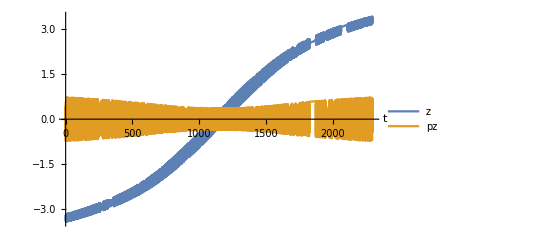
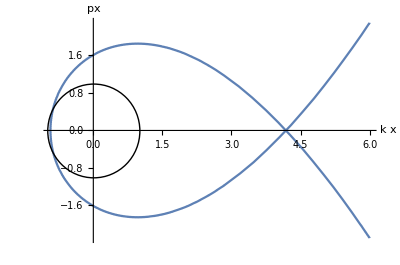

```mathematica
(*Block[{tmax=2^14},
initialPoint=allPointsDS//Select[#numUBndPoints==2&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

### Results

When launched below the neutral plane, all transient (no trapped) particles 
(*When launched above the neutral plane, all particles are trapped (no transient that will cross the neutral plane )*)

### Launched with p_x=0

When averaging over z, p_x=0 -> v_x=0

```mathematica
(*initPoints=Table[
Block[{x0=x0Temp,px0=0},
tempEqs=(rawH/. {kx->k x0,px->px0})==erg;
getInitialPoints[InitialPoints->4]
],
{x0Temp,Range[-0.99,0.99,0.2]/k}
]//Apply[Join]//RandomSample;*)
```

```mathematica
(*allPointsDS=Block[{farBoundary=6},
getPoints[initPoints,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnDataset->True]
];*)
```

```mathematica
(*plotArea[allPointsDS,TrappedStandard->1]*)
```

#### Inspect some trajectories

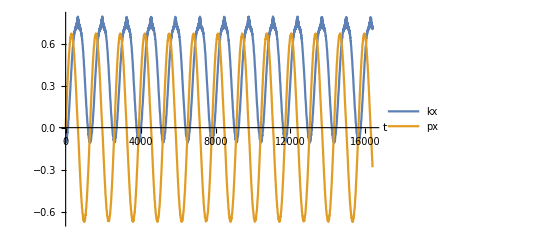
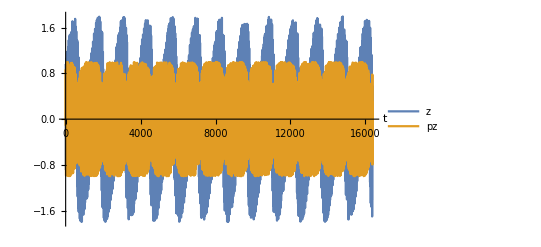
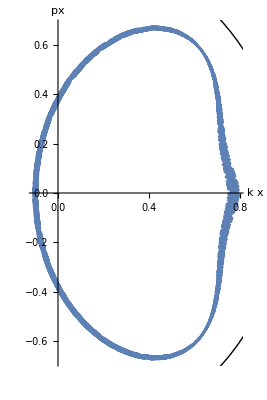

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints==0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

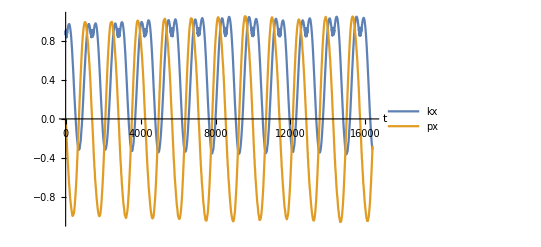
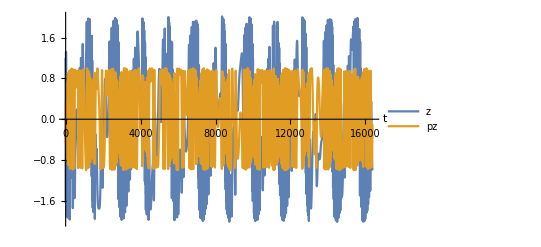
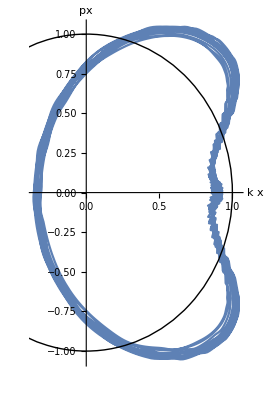

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop==False&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

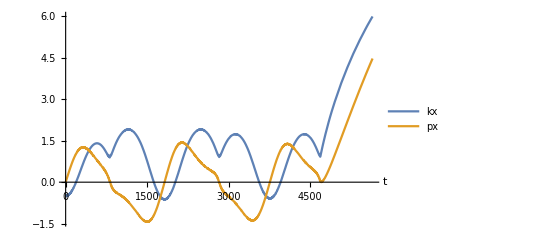
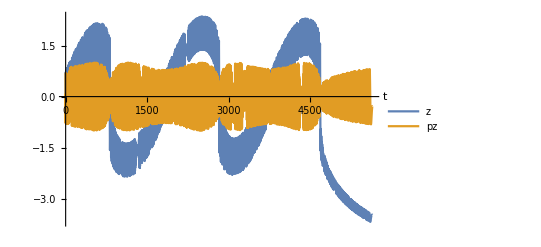
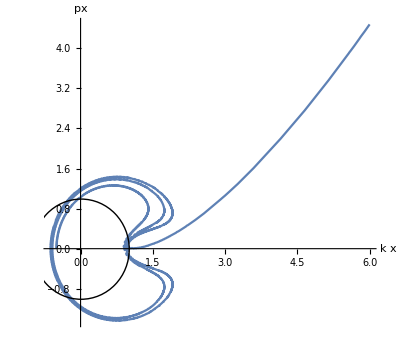

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop>0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

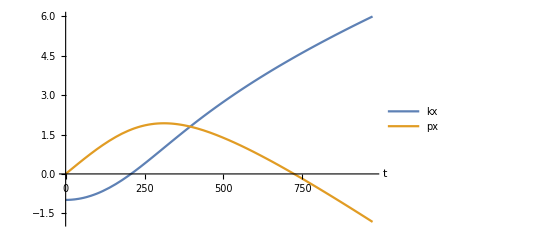
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints==1&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

## Exp 01 (Base case, Anton 2013)

```mathematica
(*c1=1/2;
c2=0;*)
```

### Pre Analysis

```mathematica
(*Block[{},
sol=SolveValues[
(∂_z U==0)&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
ParametricPlot[sol,{zc,-3,3},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1,N@c2]]//Print;
]*)
```

-Graphics-

### Launched from neutral plane : z=0

```mathematica
(*<<utilities.wl*)
```

```mathematica
(*Block[{z0=0,farBoundary=6},
tempEqs=(rawHH/. {z->z0})==erg;
allPointsDS=getPoints[InitialPoints->32,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnDataset->True];
]*)
```

```mathematica
(*(allPointsDS//Select[#stop==False&])[All,"nunmXTurningPoints"]//DeleteDuplicates//Normal
(allPointsDS//Select[#stop>0&])[All,"nunmXTurningPoints"]//DeleteDuplicates//Normal

(allPointsDS//Select[#stop==False&])[All,"numUBndPoints"]//DeleteDuplicates//Normal
(allPointsDS//Select[#stop>0&])[All,"numUBndPoints"]//DeleteDuplicates//Normal*)
```

{31,28,33,35,42,23,29,36,30,38,25,27,22,32}

{4,7,0,1,2,18}

{0,145,214,51,72,21,144,35,46,60,54,45,17,216,80}

{7,3,1,15}

```mathematica
(*plotArea[allPointsDS,TrappedStandard->1]*)
```

-Graphics-

#### Inspect some trajectories

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints==0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol,PlotVy->True]
]*)
```

-Graphics-

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints==1&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol,PlotVy->True]
]*)
```

-Graphics-

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop==False&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol,PlotVy->True]
]*)
```

-Graphics-

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop>0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol,PlotVy->True]
]*)
```

-Graphics-

#### Probability of crossing uncertainty curve

Start from same (x, p_x) with small difference in fast variables (z, p_z)

```mathematica
(*tempSol=SolveValues[(D[U,z]==0)&&D[U,{z,2}]<0&&(rawH==1/2)/. {z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}];
uncertaintyCurve=ParametricPlot[tempSol,{zc,-3,3},PlotStyle->Directive[Dashed,Black]];*)
```

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop>0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True]["solution"];
overviewPlot[sol]//Print;

izt=izTInterpolation[sol];
kxpxPlot=ParametricPlot[Evaluate[{k x[t],px[t]}/. sol],Evaluate@tRange,
AxesLabel->{"k x","px"},
ColorFunction->Function[{x,y,t},ColorData["Rainbow"][izt@t]],ColorFunctionScaling->False,
Epilog->Circle[{0,0}]];

kxpxPlot=ParametricPlot[Evaluate[{k x[t],px[t]}/. sol],Evaluate@tRange,AxesLabel->{"k x","px"},ColorFunction->Function[{x,y,t},ColorData["Rainbow"][izt@t]],ColorFunctionScaling->False];

Legended[Show[kxpxPlot,uncertaintyCurve[]],BarLegend["Rainbow",LegendLabel->"Iz"]]
]*)
```

-Graphics-

-Graphics-

Use accuracy (absolute error) as the basis for error control in solving an ODE

```mathematica
(*Block[{farBoundary=6},
initialPoint=allPointsDS//Select[#numUBndPoints>=2&]//Select[#stop>0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True,ReturnSolution->True,PrecisionGoal->∞]["solution"];
overviewPlot[sol]//Print;

izt=izTInterpolation[sol,500];
kxpxPlot=ParametricPlot[Evaluate[{k x[t],px[t]}/. sol],Evaluate@tRange,
AxesLabel->{"k x","px"},
ColorFunction->Function[{x,y,t},ColorData["Rainbow"][izt@t]],ColorFunctionScaling->False];

Legended[Show[kxpxPlot,uncertaintyCurve[]],BarLegend["Rainbow",LegendLabel->"Iz"]]
]*)
```

-Graphics-

-Graphics-

### Launched above neutral plane : z>0

```mathematica
(*x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z>0;
allPointsDS=getPoints[ReturnDataset->True];*)
```

```mathematica
(*plotArea[allPointsDS]*)
```

#### Inspect some trajectories

```mathematica
(*initialPoint=allPointsDS//Select[#numUBndPoints>2&]//Select[#stop==False&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol];
initialPoint=allPointsDS//Select[#numUBndPoints>2&]//Select[#stop>0&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol];*)
```

-Graphics-

-Graphics-

### Launched below neutral plane: z<0

```mathematica
(*x0=6/k;
tempEqs=(rawH/. {kx->k x0})==erg&&z<0;
allPointsDS=getPoints[ReturnDataset->True];*)
```

```mathematica
(*plotArea[allPointsDS]*)
```

No non-stop particles

No trapped particles

-Graphics-

#### Inspect some trajectories

```mathematica
(*Block[{tmax=2^14},
initialPoint=allPointsDS//Select[#numUBndPoints==2&]//First//Part[#,"initialPoint"]&//Normal;
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol];
]*)
```

{-Graphics-,-Graphics-,-Graphics-}

### Results

All trapped (no transient) particles when launched above the neutral plane
All transient (no trapped) particles when launched below the neutral plane

## Parameter Scanning of α

```mathematica
(*SetOptions[getPoint,StopAtInitialBoundary->False,StopAtFarBoundary->True];*)
```

## Exp 03 (α = 10)

### Numerical Solving

```mathematica
(*allPointsDS=Block[{α=10,farBoundary=4},
initPoints=Table[
Block[{x0=x0Temp,px0=0},
tempEqs=(rawH/. {kx->k x0,px->px0})==erg;
getInitialPoints[]
],
{x0Temp,Range[-0.9,0.9,0.1]/k}]//Apply[Join]//RandomSample;
getPoints[initPoints,ReturnDataset->True]
];*)
```

### PoincareMap

```mathematica
(*plotArea[allPointsDS]*)
```

-Graphics-

-Graphics-

```mathematica
(*results=nDataset[allPointsDS]
nDatasetPlot[results]*)
```

Dataset[<>]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## Exp 01 - Base Case(α = 1)

### ContourPlot

```mathematica
(*Block[{α=1},
ContourPlot[Length@NSolveValues[rawH==erg/. {kx->kxTemp,px->pxTemp,pz->0},z,Reals],{kxTemp,-1,6},{pxTemp,-3,3},
Contours->{0,1,2,3,4},ContourShading->{None,Gray,None,Yellow,None,Red}
]]*)
```

-Graphics-

```mathematica
(*Transient trajectories*)
```

### Numerical Solving

```mathematica
(*allPointsDS=Block[{α=1,farBoundary=6},
initPoints=Table[
Block[{x0=x0Temp,px0=0},
tempEqs=(rawH/. {kx->k x0,px->px0})==erg;
getInitialPoints[]
],
{x0Temp,Range[-0.9,0.9,0.1]/k}]//Apply[Join]//RandomSample;
getPoints[initPoints,ReturnDataset->True]
];*)
```

### PoincareMap

```mathematica
(*plotArea[allPointsDS]*)
```

-Graphics-

-Graphics-

```mathematica
(*results=nDataset[allPointsDS]
nDatasetPlot[results]*)
```

Dataset[<>]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## Exp 02

```mathematica
(*allPointsDS=Block[{α=0.1},
initPoints=Table[
Block[{x0=x0Temp,px0=0},
tempEqs=(rawH/. {kx->k x0,px->px0})==erg;
getInitialPoints[]
],
{x0Temp,Range[-0.95,0.95,0.05]/k}]//Apply[Join]//RandomSample;
getPoints[initPoints,ReturnDataset->True]
];*)
```

```mathematica
(*plotArea[allPointsDS]*)
```

No stop particles

-Graphics-

## Obsolete code

```mathematica
(*x0List:=Range[-0.9,0.9,0.2]/k;
initPoints=x0List//ParallelMap[f,#]&//Apply[Join]//RandomSample;

f[x_]:=Block[{x0=x,px0=0,number=128},
tempEqs=(rawH/. {kx->k x0, px->px0})==erg;
reg=ImplicitRegion[tempEqs,{z,pz}];
initPoints=Join[{x0,px0},#]&/@RandomPoint[reg//DiscretizeRegion,number]
]*)
```

#### Solve

```mathematica
(*Options[getPoint]={StopAtInitialBoundary->False,StopAtFarBoundary->True};
allPoints=getPoint/@initPoints//Parallelize
allPointsDS=Dataset@KeyUnion[allPoints,<|"zPoints"->{},"pxPoints"->{}|>];*)
```

```mathematica
(**)
```

## Utilities

Some helpful functions.

## Solver

#### getInitialPoints : Get Initial Points given equations

```mathematica
(*getInitialPoints[opts:OptionsPattern[]]:=Module[{},
freeVariables=DeleteDuplicates@Cases[tempEqs,_Symbol,∞];
(*allVariables={x,px,z,pz};*)
(*fixedVariables=DeleteElements[allVariables,freeVariables];*)

reg=ImplicitRegion[tempEqs,Evaluate@freeVariables]//DiscretizeRegion;
If[OptionValue[InitialRegionPlot],
Print@Region[reg,Axes->True,AxesLabel->freeVariables]];

RandomPoint[reg,OptionValue[InitialPoints]]//
Map[AssociationThread[freeVariables,#]&]//
Map[Join[<|x->x0,px->px0,z->z0,pz->pz0|>,#]&]//Values
]

Options[getInitialPoints]={
InitialPoints->8,
InitialRegionPlot->False
};*)
```

#### getPoint : Solve the integration using initial conditions

```mathematica
(*ClearAll[getPoint]
Options[getPoint]={
ReturnSolution->False,
StopAtInitialBoundary->True,
StopAtFarBoundary->False
};
initialBoundaryRatio=1.000001;
getPoint[initPoint_,OptionsPattern[]]:=Module[{sol,points,when,stopWhen,stop=False},
(*Test for parallelization*)
(*{px0,z0,pz0}={px,z,pz}/.First@FindInstance[tempEqs,{px,z,pz},Reals];*)
(*{px0,z0,pz0}=RandomPoint@DiscretizeRegion@reg;*)

{x0,px0,z0,pz0}=initPoint;

when={
WhenEvent[z[t]==0,Sow[{k x[t],z[t],px[t],pz[t],t},"zPoints"]],
WhenEvent[(px[t])^2+(k x[t])^2==1,Sow[{k x[t],z[t],px[t],pz[t],t},"uBndPoints"]]
};

If[OptionValue[StopAtInitialBoundary],
stopWhen={
cc[0]==0,
(*WhenEvent[z[t]==0,{{cc[t]}->{1},"RemoveEvent"}],*)
(*WhenEvent[x[t]==initialBoundaryRatio x0&&cc[t]==1,{stop=t,"StopIntegration"}]*)
WhenEvent[x[t]>initialBoundaryRatio x0,{stop=t,"StopIntegration"}]
};
when=Join[when,stopWhen]
];

(*TODO*)
If[OptionValue[StopAtFarBoundary],
stopWhen=WhenEvent[k x[t]>farBoundary,stop=t;"StopIntegration"];
AppendTo[when,stopWhen]
];

{sol,points}=Reap[
NDSolve[
Join[hamiltonianEquations,initCondition,when],
{x,z,px,pz},
{t,tmin,tmax}
(*If[OptionValue[StopAtInitialBoundary],
DiscreteVariables->Element[cc,{0,1}]]*)
],
_,Rule
];

Join[
<|"stop"->stop,"initialPoint"->initPoint,"zPoints"->{},"uBndPoints"->{}|>,
Association@points,
If[OptionValue[ReturnSolution],
<|"solution"->sol|>,
<||>
]
]
]*)
```

#### getPoints : Get Points

```mathematica
(*getPoints[initPoints_List,opts:OptionsPattern[{getPoints,getPoint}]]:=Module[{points,pointsDS},

getPointTemp[initPoint_]:=getPoint[initPoint,FilterRules[{opts},Options[getPoint]]];
points=Parallelize@Map[getPointTemp,initPoints];

If[OptionValue[ReturnDataset],
pointsDS=Dataset@points;
pointsDS[All,Append[#,{
"numUBndPoints"->Length[#uBndPoints],
"uTime"->uTime[#uBndPoints]
}]&],
points
]
]

getPoints[opts:OptionsPattern[]]:=Module[{initPoints},
initPoints=getInitialPoints[];
getPoints[initPoints,opts]
]

Options[getPoints]={
ReturnDataset->True
};

uTime[uBndPoints_]:=Switch[Length@uBndPoints,0,Infinity,1,First[uBndPoints][[5]],_,(Last[uBndPoints]-First[uBndPoints])[[5]]]


(*Using `RandomPoint` directly without discretization would not work:
The specified region appears to be unbounded.Appropriate bounds will be automatically computed.Explicit bounds may be specified as a third argument*)*)
```

#### regArea

```mathematica
(*ClearAll[regArea]
trappedStandard=2;
regArea[opts:OptionsPattern[{regArea,getPoints}]]:=Module[{allPoints,transientPoints,trappedPoints,allReg,transientReg,trappedReg},

allPointsDS=getPoints[ReturnDataset->True];

allPoints=allPointsDS//Part[#,All,"zPoints"]&//Join@@#&;
transientPoints=allPointsDS//Select[#numUBndPoints<=trappedStandard&]//Part[#,All,"zPoints"]&//Join@@#&;
trappedPoints=allPointsDS//Select[#numUBndPoints>trappedStandard&]//Part[#,All,"zPoints"]&//Join@@#&;

{allReg,transientReg,trappedReg}=If[Length@#>0,
ConcaveHullMesh[#[[All,{1,3}]]//Normal],
Null]&/@{allPoints,transientPoints,trappedPoints};

Association[
"α"->α,"k"->k,"x0"->x0,"kx"->k x0,
"allReg"->Rasterize@allReg,"areaOfAllReg"->Area@allReg,
"transientReg"->Rasterize@transientReg,"areaOfTransientReg"->Area@transientReg,
"trappedReg"->Rasterize@trappedReg,"areaOfTrappedReg"->Area@trappedReg
]
]*)
```

#### nDataset

```mathematica
(*nDataset[allPointsDS_]:=Module[{ds},
ds=Table[
Module[{pointsDS,points,avgUTime,reg},
pointsDS=allPointsDS//Select[#numUBndPoints==num&];
avgUTime=pointsDS//Part[#,All,"uTime"]&//Mean;

points=pointsDS//Part[#,All,"zPoints"]&//Join@@#&;

reg=If[Length@points!=0,
ConcaveHullMesh[points[[All,{1,3}]]//Normal]];

<|"numUBndPoints"->num,"reg"->Rasterize@reg,"area"->Area@reg,"avgUTime"->avgUTime|>
],

{num,allPointsDS[All,"numUBndPoints"]//DeleteDuplicates//Normal}
]//Dataset//Sort;

ds[All,Append[#,{
"avgAreaByNum"->If[#numUBndPoints!=0,#area/#numUBndPoints,Null],
"avgAreaByUTime"->If[#avgUTime!=0,#area/#avgUTime,Null],
"avgUTimeByNum"->If[#numUBndPoints!=0,#avgUTime/#numUBndPoints,Null]
}]&]
]*)
```

## Plot

#### overviewPlot : Overview plot for a single particle

```mathematica
(*izPlot:=Module[{tpoints,tRange,tmin,tmax,tt,ergT,Iz,td},
tpoints=200;
	
tRange:=Flatten[{t,x["Domain"]/.s}];
tmin=tRange[[2]];
tmax=tRange[[3]];
tt=Range[tmin,tmax,(tmax-tmin)/tpoints];


ergT=First@(H/.{x[t]->(x[#]/.s),z[t]->(z[#]/.s),px[t]->(px[#]/.s),pz[t]->(pz[#]/.s)})& /@tt;
Iz=Area[
ImplicitRegion[First[H/.{x[t]->(x[#]/.s),px[t]->(px[#]/.s)}]≤erg,{z[t],pz[t]}
]
]& /@tt;

td=TemporalData[{ergT,Iz},{tt}];
ListPlot[td,PlotLegends->{"Erg", "I_z"},AxesLabel->Automatic,PlotRange->All]
];*)
```

```mathematica
(*plot:=Module[{},
Print@{
α,
plot1,
plot2,
plot3,
izPlot
};
]
block:=(
Echo[α,"α:"];
solve;
plot;
)*)
```

#### poincaréMap : Plot poincaréMap

```mathematica
(*Options[poincaréMap]={"PlotAll"->False};
poincaréMap[points_,OptionsPattern[]]:=Module[{},

allPlot:=Module[{},
plot1=ListPointPlot3D[points[[All,{1,3,4}]],AxesLabel->{"k x", "px", "pz"},AspectRatio->1,PlotRange->All];
plot2=ListPlot[points[[All,{1,3}]],AxesLabel->{"k x", "px"},AspectRatio->1,PlotRange->All];
plot3=ListPlot[points[[All,{1,4}]],AxesLabel->{"k x", "pz"},AspectRatio->1,PlotRange->All];
plot4=ListPlot[points[[All,{3,4}]],AxesLabel->{"px", "pz"},AspectRatio->1,PlotRange->All];
{plot1,plot2,plot3,plot4}
];

simplePlot:=ListPlot[points[[All,{1,3}]],AxesLabel->{"k x", "px"},AspectRatio->1,PlotRange->All];

If[OptionValue["PlotAll"],allPlot,simplePlot]
]*)
```

#### plotArea : Plot Regular, Trapped And Transient Area

```mathematica
(*Options[plotArea]={
TrappedStandard->2,
Plot03->False
};

plotArea[allPointsDS_,opts:OptionsPattern[]]:=Module[{trappedPoints,transientPoints,regularPoints,zPoints,nonStopPoints,stopPoints,zzPoints,plotList},

trappedPoints:=allPointsDS//Select[#numUBndPoints>OptionValue[TrappedStandard]&]//Part[#,All,"zPoints"]&//Apply[Join];
transientPoints:=allPointsDS//Select[0<#numUBndPoints<=OptionValue[TrappedStandard]&]//Part[#,All,"zPoints"]&//Apply[Join];
regularPoints:=allPointsDS//Select[#numUBndPoints==0&]//Part[#,All,"zPoints"]&//Apply[Join];
zPoints=Select[<|"Regular"->regularPoints[[All,{1,3}]],"Trapped"->trappedPoints[[All,{1,3}]],"Transient"->transientPoints[[All,{1,3}]]|>,Length@#>0&];

nonStopPoints:=allPointsDS//Select[#stop==False&]//Part[#,All,"zPoints"]&//Apply[Join];
stopPoints:=allPointsDS//Select[#stop>0&]//Part[#,All,"zPoints"]&//Apply[Join];
zzPoints=Select[<|"Stopped"->stopPoints[[All,{1,3}]],"Non-Stopped"->nonStopPoints[[All,{1,3}]]|>,Length@#>0&];

plot01:=ListPlot[zzPoints,
PlotLabel->"Categorized by stop or not",
AxesLabel->{"κ x","p_x"},AspectRatio->1];
plot02:=ListPlot[zPoints,
PlotLabel->"Categorized by num of uncertain points",
AxesLabel->{"κ x","p_x"},AspectRatio->1];

plot03:=ListPlot[
allPointsDS[All,{"numUBndPoints"->ToString}][GroupBy["numUBndPoints"],Apply[Join],"zPoints",Part[#,All,{1,3}]&]//Select[Length@#>0&],
AxesLabel->{"κ x","p_x"},AspectRatio->1,
PlotLabel->"Categorized by num of uncertain points",
PlotLegends->PointLegend[Automatic,LegendLabel->"Num of uncertain points"]
];

plotList={};
If[Length@zzPoints!=0,
plot01//AppendTo[plotList,#]&
];

If[Length@zPoints!=0,
plot02//AppendTo[plotList,#]&
];

If[OptionValue[Plot03],
plot03//Rasterize//Print
];

If[Length@nonStopPoints==0,
Echo["No non-stop particles"]
];
If[Length@stopPoints==0,
Echo["No stop particles"]
];
If[Length@transientPoints==0,
Echo["No transient particles"]
];
If[Length@trappedPoints==0,
Echo["No trapped particles"]
];

GraphicsRow[Rasterize/@plotList]
]*)
```

#### nDatasetPlot

```mathematica
(*nDatasetPlot[results_]:=Module[{},
p1=ListPlot[{
results[[All, {"numUBndPoints", "area"}]] // Normal // Values,
results[[All, {"numUBndPoints", "avgAreaByNum"}]] // Normal // Values
},
AxesLabel -> {"numUBndPoints (n)", "Area (A)"},
PlotLegends -> {"Total Area", "Average Area by n"}
];

p2=ListPlot[
results[[All, {"numUBndPoints", "avgAreaByNum"}]] ,
AxesLabel -> {"numUBndPoints (n)", "Area (A)"},
PlotLegends -> { "Average Area by n"}
];

p3=ListLogPlot[{
results[[All, {"numUBndPoints", "avgUTime"}]]  // Normal // Values,
results[[All, {"numUBndPoints", "avgUTimeByNum"}]]  // Normal // Values
},
AxesLabel -> {"n", "Time"},
PlotLegends -> {"Avg UTime", "Avg UTime by n"}
];

p4=ListLogPlot[
results[[All, {"numUBndPoints","avgAreaByUTime"}]],
AxesLabel -> {"n", "Area"},
PlotLegends -> { "Average Area by Average uTime"}
];

Echo[results//Select[#numUBndPoints==trappedStandard&]//Part[#,All,"avgAreaByUTime"]&//Total,"Transient-type Average Area by Time"];
Echo[results//Select[#numUBndPoints!=trappedStandard&]//Part[#,All,"avgAreaByUTime"]&//Total,"Other-type  Average Area by Time"];

Print/@{p1,p2,p3,p4};
]*)
```

## Case Study: trajectories

We assume κ is 0.01 for all the cases below.

```mathematica
(*(*InitialPoints is set 16 so that include both transient and trapped particles.*)
SetOptions[getInitialPoints,InitialPoints->16];
SetOptions[getPoint,StopAtInitialBoundary->True,StopAtFarBoundary->False,ReturnSolution->False];*)
```

### α = 1 (Base case)

```mathematica
(*αTemp=1; 
c1=1;
c2=1;*)
```

#### Get enough trajectories

```mathematica
(*allPointsDS=Block[{α=αTemp,x0=6./k},
tempEqs=(rawH==erg/. {kx->k x0})&&z<0;
getPoints[ReturnDataset->True,InitialPoints->64]
]*)
```

#### Transient trajectories

```mathematica
(*initialPoint=allPointsDS//Select[#numUBndPoints==2&]//First//Part[#,"initialPoint"]&//Normal;
Block[{α=αTemp},
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True]
]*)
```

#### Trapped trajectories

No trapped trajectories

```mathematica
(*initialPoint=allPointsDS//Select[#numUBndPoints>2&]//First//Part[#,"initialPoint"]&//Normal//Echo;*)
(*initialPoint={600.,3.416867062269855,-3.594552096183053,-0.5051207049102734};
Block[{α=αTemp},
pointInfo= getPoint[initialPoint,ReturnSolution->True];
sol =pointInfo["solution"];
overviewPlot[sol,Plot3D->True]
]*)
```

#### Uncertainty curve intersection

```mathematica
solCurve=Block[{c1=1,c2=1,α=1},
SolveValues[
(D[U, z]==0)&&D[U,{z,2}]<=0&&
(rawH==1/2)/.{z->zc,pz->0,kx->kxs,px->pxs},{kxs,pxs}]
]
```

{{ConditionalExpression[-(-12 zc+2 zc^3-zc^5+12 (1/6 (6 zc-zc^3)-2 √(zc^2/(4+zc^4)))-6 zc^2 (1/6 (6 zc-zc^3)-2 √(zc^2/(4+zc^4))))/(12 zc), 0<zc<Root1.11Root[-64+32 #1^2+12 #1^6+#1^10&,2]1.106714811898014],ConditionalExpression[1/6 (6 zc-zc^3)-2 √(zc^2/(4+zc^4)), 0<zc<Root1.11Root[-64+32 #1^2+12 #1^6+#1^10&,2]1.106714811898014]},{ConditionalExpression[-(-12 zc+2 zc^3-zc^5+12 (1/6 (6 zc-zc^3)+2 √(zc^2/(4+zc^4)))-6 zc^2 (1/6 (6 zc-zc^3)+2 √(zc^2/(4+zc^4))))/(12 zc), Root-1.11Root[-64+32 #1^2+12 #1^6+#1^10&,1]-1.106714811898014<zc<0],ConditionalExpression[1/6 (6 zc-zc^3)+2 √(zc^2/(4+zc^4)), Root-1.11Root[-64+32 #1^2+12 #1^6+#1^10&,1]-1.106714811898014<zc<0]}}

```mathematica
tRange=Flatten[{t,x["Domain"]/.sol}];
plot01=ParametricPlot[Evaluate[{k x[t],px[t]}/.sol],Evaluate@tRange,AxesLabel->{"k x", "px"},PlotRange->Full];
plot02=ParametricPlot[solCurve,{zc,-3,3},PlotStyle->{Orange,Thick}]
plot03=Show[plot01,plot02]
selfIntersections=Graphics`Mesh`FindIntersections[plot01];
allIntersections=Graphics`Mesh`FindIntersections[plot03];
Complement[allIntersections,selfIntersections]
```

-Graphics-

-Graphics-

{{0.967304,0.0475472},{0.982775,-0.0319469},{0.998229,0.0065304},{0.99938,-0.00302737},{1.,-2.95606×10^-17}}

### α = 10

```mathematica
αTemp=10;
```

#### ContourPlot

```mathematica
Block[{α=αTemp},
ContourPlot[Length@NSolveValues[rawH==erg/. {kx->kxTemp,px->pxTemp,pz->0},z,Reals],{kxTemp,-1,4},{pxTemp,-3,3},
Contours->{0,1,2,3,4},ContourShading->{None,Gray,None,Yellow,None,Red}
]]
```

-Graphics-

#### Get enough trajectories

```mathematica
allPointsDS=Block[{α=αTemp,x0=4./k},
tempEqs=(rawH==erg/. {kx->k x0})&&z<0;
getPoints[ReturnDataset->True]
]
```

#### Transient trajectories

```mathematica
initialPoint=allPointsDS//Select[#numUBndPoints==2&]//First//Part[#,"initialPoint"]&//Normal;
Block[{α=αTemp},
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True]
]
```

-Graphics-

#### Trapped trajectories

```mathematica
initialPoint=allPointsDS//Select[#numUBndPoints>2&]//First//Part[#,"initialPoint"]&//Normal;
Block[{α=αTemp},
sol = getPoint[initialPoint,ReturnSolution->True]["solution"];
overviewPlot[sol,Plot3D->True]
]
```

-Graphics-

## Archives Codes

#### ContourPlot

```mathematica
(*Block[{α=αTemp},
ContourPlot[Length@NSolveValues[rawH==erg/. {kx->kxTemp,px->pxTemp,pz->0},z,Reals],{kxTemp,-1,6},{pxTemp,-3,3},
Contours->{0,1,2,3,4},ContourShading->{None,None,None,Gray,None,Yellow},MaxRecursion->3,
FrameLabel->{"κ x", "p_x"}
]]*)
```

-Graphics-